# Compiling Matmul to Blocks and Tiles, Version 2

## Technical Report, GSI Technology, Preliminary Draft

Brian Beckman
Technology Fellow, GSI Technology
November, 2023

## Abstract

This is an executable design specification. It is straightforward to transcribe its proofs and prototypes from Wolfram language to any ordinary programming language of your choice.

The layout problem answers “how to rearrange matrices to fit the APU?” Consider domain matrices, A[m,k] and B[k,n], of arbitrary but compatible dimensions, meaning that the column count, k, of A equals the row count, k, of B. Due to compatibility, the non-commutative matrix product A.B is sensible. Now consider the Gemini-I APU, which has a main memory (MMB) of 24×VR bits, where a VR is 64 HBs and an HB (half-bank) is 2048×16 bits. The Gemini-I APU also has 53 VRs worth of space in L1 cache (parity off). The layout problem for matrix multiplication is finding an optimal procedure for dynamically loading, multiplying, and storing non-overlapping partitions of A and B in the APU’s L1 cache and main memory. The solution to the layout problem includes finding optimal sizes of blocks and tiles and optimal sequences of operations for moving and multiplying blocks and tiles. Blocks are optimized to fit L1. tiles are optimized to fit main memory, where multiplication occurs. Optimal means with minimum running time. Compile time is not considered. Running time includes the time for I/O between L1 and main memory but not I/O to a host computer.

At first glance, the layout problem seems like a constrained combinatorial optimization problem, thus difficult to pose well and expensive to solve. This paper by Kuzma et al. (https://arxiv.org/pdf/2305.18236.pdf) presents optimal partitioning of matrices into blocks and blocks into tiles at compile time. We investigate Kuzma’s algorithm in this paper, first by reproducing Kuzma’s original example, then by adapting that example to the APU.

## Accumulated Outer Product

First, we note that accumulated outer product is preferable to iterated inner product for all dimensions >1. This fact justifies the inner-most routine shown below, tileMul.

```mathematica
ClearAll[row,col];
row[M_,i_]:=M[[i]];
col[M_,i_]:=Mᵀ[[i]]ᵀ;
```

```mathematica
ClearAll[iteratedInnerProduct,accumulatedOuterProduct,builtInProduct];
iteratedInnerProduct[m_,k_,n_,A_,B_]:=
Module[{i,j,ab=ConstantArray[0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[i=1,i<=m,i++,
For[j=1,j<=n,j++,
ab[[i,j]]=row[A,i].col[B,j]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
accumulatedOuterProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab=ConstantArray[0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[kk=1,kk<=k,kk++,
ab+=Outer[Times,col[A,kk],row[B,kk]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
builtInProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab,result,time},
{time,result}=AbsoluteTiming[ab=A.B];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
```

### Large Matrices

```mathematica
On[Assert];
```

```mathematica
ClearAll[timings];
(timings=With[{precision=1.*^-5},
Module[{timings=
Table[With[{m=d,k=d,n=d},
With[{A=RandomReal[{0.,1.},{m,k}],
B=RandomReal[{0.,1.},{k,n}]},
<|"dim"->d,
"built-in"->builtInProduct[m,k,n,A,B],
"inner"->iteratedInnerProduct[m,k,n,A,B],
"outer"->accumulatedOuterProduct[m,k,n,A,B]|>
]],{d,1,200,25}]},
Map[Assert[
Round[#["built-in"]["result"],precision]===
Round[#["inner"]["result"],precision]===
Round[#["outer"]["result"],precision]
]&,timings];
Map[{#["dim"],#["built-in"]["time"],#["inner"]["time"],#["outer"]["time"]}&,timings]
]])//MatrixForm
```

(1 | 7.×10^-6 s | 0.000021 s | 0.000015 s
26 | 0.000015 s | 0.001694 s | 0.000082 s
51 | 0.000014 s | 0.008331 s | 0.000244 s
76 | 0.000246 s | 0.027375 s | 0.000636 s
101 | 0.000911 s | 0.059154 s | 0.001963 s
126 | 0.000083 s | 0.120059 s | 0.003073 s
151 | 0.000099 s | 0.186912 s | 0.004844 s
176 | 0.000166 s | 0.20466 s | 0.005295 s)

```mathematica
ClearAll[plottableTimings];
plottableTimings[j_]:={col[timings,1],(Log10@*QuantityMagnitude)[col[timings,j]]}ᵀ
```

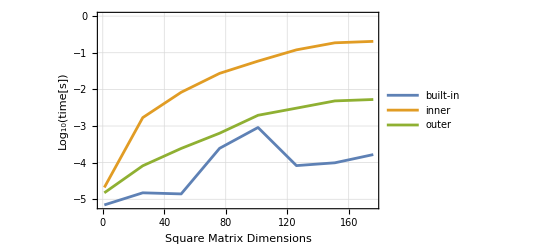

```mathematica
ListLinePlot[{plottableTimings[2],
plottableTimings[3],plottableTimings[4]},
(*ImageSize->Large,*)GridLines->Automatic,
Frame->True,PlotLegends->{"built-in","inner","outer"},
FrameLabel->{{"Log_10(time[s])",""},{"Square Matrix Dimensions","Running Times"}}]
```

## Table 1 — VSR and ACC

Kuzma presents a worked-out example for his IBM POWER10 MMA chip, which has VSRs of 128 bits and ACCs of 512 bits. The bits in these registers can handle seven different types of elements. The computation size in the table implies tile sizes m×k and k×n that produce results that fit in an ACC of 512 bits. The first worked example below approximates this with tiles of small size that can be visually checked in the paper. Tiles in the APU are much larger, 1×2048 for example and more difficult to visualize. Therefore, we present examples with large APU tiles after we have vetted the algorithm.

```mathematica
ClearAll[mmaI,mmaI4,mmaI8,mmaI16,mmaBf16,mmaF16,mmaF32,mmaF64];
```

The integer MMA instructions for the POWER10 consume four 128-bit VSRs — an ACC, for a total of 512 bits. Up to 32 VSRs can be used, 4 at a time, in this way.

```mathematica
mmaI[bitCount_?(MemberQ[{4,8,16},#]&)]:=
With[{m=4,k=32/bitCount,n=4},
With[{A=RandomInteger[{0,2^bitCount-1},{m,k}],
B=RandomInteger[{0,2^bitCount-1},{k,n}]},
accumulatedOuterProduct[m,k,n,A,B]]]
```

```mathematica
mmaI[8]
```

<|m→4,k→4,n→4,result→{{26204,52112,69264,49795},{45357,84485,115059,59390},{50454,71176,112401,87412},{22549,21229,44103,47054}},time→0.000029 s|>

accumulatedOuterProduct also works as a rank-1 outer product.

```mathematica
accumulatedOuterProduct[5,1,4,({{1}, {2}, {3}, {4}, {5}}),({{7, 11, 13, 19}})]["result"]//MatrixForm
```

(7 | 11 | 13 | 19
14 | 22 | 26 | 38
21 | 33 | 39 | 57
28 | 44 | 52 | 76
35 | 55 | 65 | 95)

## Codegen for GEMM

GEMM is a standard operation in LAPACK.

### Algorithm 1

A, B, APack, BPack, AccTile, ATile, BTile, ABTile, CTile, and CNewTile are free-variable pointers to memory. nr , kr, mr are free packing parameters. In my opinion, they would be better called tiling parameters because they’re tuned to the intrinsic LLVM on line 12, but I’ll follow the paper’s nomenclature for now. nc, kc, mc are free blocking parameters that divide matrices into blocks appropriately sized and ordered (row-major versus column-order) for cache. lda, ldb, ldc are free leading dimensions, thus strides, and pertain to either row-major or column-major storage conventions. The pack function reorders blocks into row-major or column-major order as needed for optimal tile-multiplication speed. α and β are free scalar parameters required by GEMM. My implementation refactors Algorithm 1 for greater clarity. Later, we show a direct transcription of Algorithm 1 and compare it to our refactored form.

```mathematica
ClearAll[packingParameters,mr,kr,nr,blockingParameters,mc,kc,nc,A,APack,B,BPack,leadingDimensions,lda,ldb,ldc,ATile,BTile,AccTile,ABTile,CTile,CNewTile,β,α];
packingParameters={mr,kr,nr};
blockingParameters={mc,kc,nc};
leadingDimensions={lda,ldb,ldc};
```

M, K, N are original dimensions: M×K for AOriginal, K×N for BOriginal. kc (block size) must divide K; mc (block size) must divide M, nc (block size) must divide N. If not, the original matrices, AOriginal and BOriginal, must be padded out with zeros to integer multiples of mc, kc, nc. Such is preprocessing, not described here. Likewise, mr (tile size) must divide mc, kr (tile size) must divide kc, and nr (tile size) must divide nc.

In the following illustration, AOriginal and BOriginal are stored in column-major order.

Let us mechanize a concrete version of this illustration by ignoring most ellipses (triple dots). An exception is the picture of B, for which we increase kc from 2kr to 3kr for consistency with the picture of A. The two pictures for A and for B represent the (4,2) and (2,2) 1-indexed blocks, respectively, of the original matrices, AOriginal and BOriginal.

## Compiling MatMul to Blocks and Tiles

### tileMul

Everything gets compiled to calls of tileMul. This is our refactored stand-in for the loop over llvm.matrix.multiply on lines 9 through 13 of Algorithm 1. Our stand-in for llvm.matrix.multiply itself is an invocation of Mathematica’s built-in Dot operator.

tileMul multiplies blocks that contain small tiles, multiplying each tile at maximum speed in the machine. A tile is a sub-matrix that snugly fits in the particular machine registers used for multiplication. tileMul is here parameterized to the dimensions of blocks and tiles so that we can compile to various devices, such as the Gemini-I APU and the Gemini-II APU, which differ in dimensions.

tileMul takes a pair of blocks with snug tiles inside, then triples of integers for inner and outer dimensions. The three outer dimensions, mc, kc, and nc, are dimensions of block multiplicands, mc×kc and kc×nc. The three inner dimensions, mr, kr, and nr, are dimensions of tile multiplicands, mr×kr and kr×nr. Each inner dimension must evenly divide the corresponding outer dimension, meaning that tiles must partition blocks, that is, fit in blocks with no gaps or overlaps. The number of block rows must be an integer multiple of the number of tile rows, and likewise for columns. Each of mc/mr, kc/kr, and nc/nr must be integers.

As an illustration, consider the following two tiled blocks.

```mathematica
aBlockTiled$=({{({{15, 14, 10, 15}, {3, 9, 8, 5}}), ({{6, 0, 3, 8}, {5, 10, 9, 6}}), ({{3, 14, 1, 1}, {6, 1, 14, 4}})}, {({{11, 14, 9, 10}, {11, 13, 3, 3}}), ({{12, 2, 0, 15}, {5, 3, 15, 13}}), ({{5, 4, 14, 1}, {13, 4, 7, 3}})}, {({{12, 7, 14, 14}, {15, 6, 14, 13}}), ({{2, 7, 15, 15}, {1, 13, 0, 8}}), ({{5, 0, 9, 1}, {14, 5, 2, 10}})}});
bBlockTiled$=({{({{9, 4}, {4, 1}, {11, 9}, {15, 3}}), ({{9, 13}, {14, 12}, {9, 13}, {12, 13}}), ({{6, 7}, {7, 11}, {10, 3}, {7, 15}}), ({{12, 3}, {8, 4}, {0, 13}, {3, 12}}), ({{4, 11}, {8, 11}, {5, 4}, {5, 5}})}, {({{13, 15}, {14, 2}, {0, 13}, {10, 0}}), ({{7, 0}, {10, 15}, {3, 15}, {8, 7}}), ({{1, 4}, {6, 6}, {15, 6}, {11, 7}}), ({{15, 5}, {11, 6}, {15, 6}, {11, 11}}), ({{5, 8}, {14, 10}, {8, 15}, {5, 15}})}, {({{3, 14}, {10, 10}, {7, 5}, {10, 8}}), ({{0, 3}, {14, 5}, {6, 1}, {0, 3}}), ({{5, 3}, {9, 7}, {13, 2}, {14, 12}}), ({{5, 2}, {11, 15}, {1, 10}, {7, 5}}), ({{9, 12}, {11, 0}, {2, 7}, {8, 6}})}});
```

The outer dimensions of the pair (aBlockTiled$, bBlockTiled$) are mc=(3×(mr=2))=6 (three rows of 2-row tiles in aBlockTiled$), kc=(3×(kr=4))=12 (three columns of 4-column tiles in aBlockTiled$, and three rows of 4-row tiles in bBlockTiled$), and nc=(5×(nr=2))=10 (five columns of 2-column tiles in bBlockTiled$). The inner dimensions are mr=2, kr=4, nr=2, corresponding respectively to the row dimension, mr, of a left-multiplicand tile; to the column dimension, kr, of a left-multiplicand tile, equal to the row dimension of a right-multiplicand tile; and to the column dimension, nr, of a right-multiplicand tile.

Notice that nr must equal mr because tiles are of transposed shapes on the left and the right of our tile product. This restriction does not pertain to Kuzma’s original Algorithm 1, only to our refactoring of it. The API has separate parameters for them for the sake of symmetry in the API, making it easier to remember.

Define tileMul as an iterated inner product of tiles and accumulated outer product within the tiles, then apply it to these examples:

```mathematica
ClearAll[tileMul];
tileMul[ATiles_,BTiles_,mc_,kc_,nc_,mr_,kr_,nr_]:=
Module[{tm,tk,tn,CTile,McByMr=mc/mr,KcByKr=kc/kr,NcByNr=nc/nr},
CTile=ConstantArray[ConstantArray[0,{mr,nr}],{McByMr,NcByNr}];
For[tm=1,tm<=McByMr,tm++,(* for each row of A's tiles *)
For[tn=1,tn<=NcByNr,tn++,(* for each column in B's tiles *)
For[tk=1,tk<=KcByKr,tk++,(* iterated inner products of tiles *)
(* ATiles⟦tm,tk⟧.BTiles⟦tk,tn⟧ implicitly by accumulated outer product *)
CTile[[tm,tn]]+=ATiles[[tm,tk]].BTiles[[tk,tn]]]]];
CTile];
```

```mathematica
tileMul[aBlockTiled$,bBlockTiled$,6,12,10,2,4,2]//MatrixForm
```

((850 | 533
657 | 516) | (918 | 872
593 | 692) | (700 | 733
739 | 496) | (737 | 778
592 | 601) | (582 | 696
541 | 748)
(901 | 541
624 | 650) | (860 | 745
656 | 813) | (770 | 656
833 | 610) | (731 | 778
858 | 607) | (539 | 866
629 | 1004)
(862 | 585
989 | 608) | (803 | 1066
784 | 968) | (949 | 703
811 | 747) | (780 | 826
710 | 751) | (618 | 1000
735 | 852))

To check this result against a straightforward matrix product, we must flatten the tile level.

### untileBlock

Is the result above equivalent to the matrix product aBlockTiled$.bBlockTiled$? First define untileBlock, which does exactly what its name says.

```mathematica
ClearAll[untileBlock];
untileBlock[ATiledBlock_,mr_,mc_,kr_,kc_]:=
(* Produce 1 mc×kc block from its tiles, each mr×kr. *)
Module[{ABlock=ConstantArray[0,{mc,kc}],tileI,tileJ,inI,inJ,bm,bk},
For[bm=1,bm<=mc,bm++,
For[bk=1,bk<=kc,bk++,
tileI=1+Quotient[(bm-1),mr];
tileJ=1+Quotient[(bk-1),kr];
inI=1+Mod[(bm-1),mr];
inJ=1+Mod[(bk-1),kr];
ABlock[[bm,bk]]=ATiledBlock[[tileI,tileJ,inI,inJ]]]];
ABlock];
```

Apply untileBlock to aBlockTiled$ and to bBlockTiled$., compute the matrix product via Wolfram’s built-in, then visually check that the untiled matrices match their tiled brethren above.

```mathematica
(aBlock$=untileBlock[aBlockTiled$,2,6,4,12])//MatrixForm
(bBlock$=untileBlock[bBlockTiled$,4,12,2,10])//MatrixForm
(cBlock$=aBlock$.bBlock$)//MatrixForm
```

(15 | 14 | 10 | 15 | 6 | 0 | 3 | 8 | 3 | 14 | 1 | 1
3 | 9 | 8 | 5 | 5 | 10 | 9 | 6 | 6 | 1 | 14 | 4
11 | 14 | 9 | 10 | 12 | 2 | 0 | 15 | 5 | 4 | 14 | 1
11 | 13 | 3 | 3 | 5 | 3 | 15 | 13 | 13 | 4 | 7 | 3
12 | 7 | 14 | 14 | 2 | 7 | 15 | 15 | 5 | 0 | 9 | 1
15 | 6 | 14 | 13 | 1 | 13 | 0 | 8 | 14 | 5 | 2 | 10)

(9 | 4 | 9 | 13 | 6 | 7 | 12 | 3 | 4 | 11
4 | 1 | 14 | 12 | 7 | 11 | 8 | 4 | 8 | 11
11 | 9 | 9 | 13 | 10 | 3 | 0 | 13 | 5 | 4
15 | 3 | 12 | 13 | 7 | 15 | 3 | 12 | 5 | 5
13 | 15 | 7 | 0 | 1 | 4 | 15 | 5 | 5 | 8
14 | 2 | 10 | 15 | 6 | 6 | 11 | 6 | 14 | 10
0 | 13 | 3 | 15 | 15 | 6 | 15 | 6 | 8 | 15
10 | 0 | 8 | 7 | 11 | 7 | 11 | 11 | 5 | 15
3 | 14 | 0 | 3 | 5 | 3 | 5 | 2 | 9 | 12
10 | 10 | 14 | 5 | 9 | 7 | 11 | 15 | 11 | 0
7 | 5 | 6 | 1 | 13 | 2 | 1 | 10 | 2 | 7
10 | 8 | 0 | 3 | 14 | 12 | 7 | 5 | 8 | 6)

(850 | 533 | 918 | 872 | 700 | 733 | 737 | 778 | 582 | 696
657 | 516 | 593 | 692 | 739 | 496 | 592 | 601 | 541 | 748
901 | 541 | 860 | 745 | 770 | 656 | 731 | 778 | 539 | 866
624 | 650 | 656 | 813 | 833 | 610 | 858 | 607 | 629 | 1004
862 | 585 | 803 | 1066 | 949 | 703 | 780 | 826 | 618 | 1000
989 | 608 | 784 | 968 | 811 | 747 | 710 | 751 | 735 | 852)

### blockIt, tileIt

We now know how to multiply blocks full of snug tiles. We need to partition general matrices into snug blocks, in-turn partitioned into snug tiles. The dimensions of the snug blocks must divide the dimensions of the matrices, but that is the only restriction. If the matrices don’t snugly contain blocks, pad out the matrices in a pre-processing step. We do not consider that padding step in this paper.

Define a pair of functions, blockIt and tileIt, that, respectively, produce a blocked matrix and a tiled block.

```mathematica
ClearAll[blockIt,tileIt];

blockIt[A_,mc_,M_,kc_,K_]:=Table[
A[[m;;m+mc-1,k;;k+kc-1]],{m,1,M,mc},{k,1,K,kc}];

tileIt[ABlock_,mr_,mc_,kr_,kc_]:=Table[
ABlock[[m;;m+mr-1,k;;k+kr-1]],{m,1,mc,mr},{k,1,kc,kr}];
```

Iterate tileIt over the result of blockIt on a matrix to get a doubly partitioned blocked and tiled matrix. Below is an example. Notice we build the dimensions bottom-up to ensure integer divisibility and to avoid padding. The regular structure in the displays is evident and instructive. Strive to see how 2D iterations of tileMul produces desired results.

```mathematica
With[{bitCount=4},
With[{mr=2,kr=4,nr=2},(* -- tiles *)
With[{mc=2mr,kc=2kr,nc=2nr},(* mc=4, kc=8, nc=4 -- blocks *)
With[{M=2mc,K=2kc,N=2nc},(* M=8, K=16, N=8, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocked=blockIt[A,mc,M,kc,K],
BBlocked=blockIt[B,kc,K,nc,N],
ATiled,BTiled},
ATiled=Table[tileIt[ABlocked[[bm,bk]],mr,mc,kr,kc],{bm,1,M/mc},{bk,1,K/kc}];
BTiled=Table[tileIt[BBlocked[[bk,bn]],kr,kc,nr,nc],{bk,1,K/kc},{bn,1,N/nc}];
Column[{(* displays *)
ATiled//MatrixForm,
BTiled//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[A_blocked]"->Dimensions[ABlocked],
"dim[B_blocked]"->Dimensions[BBlocked],
"A_tiled"->Dimensions[ATiled],
"B_tiled"->Dimensions[BTiled],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;}]]]]]]]
```

<|dim[A]→{8,16},dim[B]→{16,8},dim[A_blocked]→{2,2,4,8},dim[B_blocked]→{2,2,8,4},A_tiled→{2,2,2,2,2,4},B_tiled→{2,2,2,2,4,2},bits→4,mr→2,kr→4,nr→2,mc→4,kc→8,nc→4,M→8,K→16,N→8|>

(((15 | 1 | 15 | 9
1 | 12 | 11 | 14) | (0 | 10 | 1 | 7
0 | 0 | 5 | 9)
(5 | 4 | 1 | 7
13 | 2 | 14 | 9) | (4 | 7 | 10 | 15
10 | 7 | 6 | 4)) | ((2 | 0 | 7 | 1
5 | 15 | 12 | 14) | (1 | 14 | 9 | 2
13 | 14 | 13 | 12)
(1 | 12 | 10 | 8
7 | 12 | 5 | 10) | (15 | 11 | 12 | 12
6 | 1 | 0 | 3))
((10 | 12 | 11 | 7
1 | 14 | 5 | 11) | (2 | 8 | 0 | 1
9 | 2 | 10 | 0)
(2 | 11 | 2 | 8
0 | 13 | 1 | 14) | (6 | 15 | 11 | 14
12 | 8 | 13 | 12)) | ((8 | 5 | 15 | 15
11 | 15 | 0 | 8) | (13 | 11 | 9 | 14
11 | 15 | 2 | 9)
(11 | 5 | 7 | 9
10 | 13 | 9 | 11) | (9 | 15 | 13 | 8
8 | 10 | 9 | 14)))
(((9 | 8
7 | 0
7 | 13
7 | 9) | (7 | 10
15 | 9
6 | 14
0 | 6)
(5 | 6
6 | 1
1 | 10
9 | 1) | (14 | 1
5 | 3
12 | 11
9 | 5)) | ((10 | 1
1 | 4
13 | 9
13 | 0) | (6 | 6
10 | 1
4 | 11
10 | 12)
(6 | 10
13 | 15
8 | 9
14 | 3) | (1 | 14
5 | 3
0 | 9
4 | 7))
((0 | 11
15 | 14
9 | 4
14 | 3) | (9 | 9
1 | 8
7 | 12
4 | 11)
(4 | 5
3 | 1
2 | 11
8 | 5) | (0 | 8
8 | 2
15 | 12
11 | 5)) | ((0 | 10
7 | 5
7 | 6
9 | 8) | (11 | 9
2 | 10
3 | 13
15 | 13)
(6 | 1
10 | 12
7 | 13
15 | 12) | (6 | 15
14 | 15
6 | 12
9 | 15)))

### unBlock

unBlock is exactly parallel to untileBlock. It does not need a unit test or an illustrative example.

```mathematica
ClearAll[unblock];

unblock[ABlocked_,mc_,M_,kc_,K_]:=
Module[{A=ConstantArray[0,{M,K}],blockI,blockJ,inI,inJ,m,k},
For[m=1,m<=M,m++,
For[k=1,k<=K,k++,
blockI=1+Quotient[(m-1),mc];
blockJ=1+Quotient[(k-1),kc];
inI=1+Mod[(m-1),mc];
inJ=1+Mod[(k-1),kc];
A[[m,k]]=ABlocked[[blockI,blockJ,inI,inJ]]]];
A];
```

### blockTileMul, blockMul

blockTileMul is the intermediate target of compilation, after matrices have been blocked and tiled as described above. blockTileMul calls tileMul at bottom.

For testing, we include a blockMul routine for blocked-but-not-tiled matrices: the untiled results of blockTileMul must match the results of blockMul, and the unblocked results must match the results of Mathematica’s built-in matrix multiplication. The following defines blockTileMul and blockMul, then Asserts the requirements on an example.

```mathematica
On[Assert];
ClearAll[blockMul,blockTileMul];

blockTileMul[ABlocks_,BBlocks_,M_,K_,N_,mc_,kc_,nc_,mr_,kr_,nr_]:=
(* ABlocks is an array of mc×kc blocks, BBlock of kc×nc blocks. *)
Module[{bm,bk,bn,MByMc=M/mc,KByKc=K/kc,NByNc=N/nc,McByMr=mc/nr,NcByNr=nc/nr,
CTiled,ATiles,BTiles},
CTiled=ConstantArray[ConstantArray[ConstantArray[0,{mr,nr}],
{McByMr,NcByNr}],{MByMc,NByNc}];
(* for each input block *)
For[bm=1,bm<=MByMc,bm++,
For[bn=1,bn<=NByNc,bn++,
(* iterated inner product *)
For[bk=1,bk<=KByKc,bk++,
ATiles=tileIt[ABlocks[[bm,bk]],mr,mc,kr,kc];
BTiles=tileIt[BBlocks[[bk,bn]],kr,kc,nr,nc];
CTiled[[bm,bn]]+=tileMul[ATiles,BTiles,mc,kc,nc,mr,kr,nr]]]];
CTiled];

blockMul[ABlocks_,BBlocks_,M_,K_,N_,mc_,kc_,nc_,mr_,kr_,nr_]:=
Module[{bm,bk,bn,MByMc=M/mc,KByKc=K/kc,NByNc=N/nc,McByMr=mc/nr,NcByNr=nc/nr,
CBlocked},
CBlocked=ConstantArray[ConstantArray[0,{mc,nc}],{MByMc,NByNc}];
(* for each input block *)
For[bm=1,bm<=MByMc,bm++,
For[bn=1,bn<=NByNc,bn++,
(* iterated inner product *)
For[bk=1,bk<=KByKc,bk++,
CBlocked[[bm,bn]]+=ABlocks[[bm,bk]].BBlocks[[bk,bn]]]]];
CBlocked];

With[{bitCount=4},
With[{mr=2,kr=4,nr=2},(* -- tiles *)
With[{mc=3mr,kc=3kr,nc=5nr},(* mc=6, kc=12, nc=10 -- blocks *)
With[{M=5mc,K=3kc,N=3nc},(* M=30, K=36, N=30, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocks=blockIt[A,mc,M,kc,K],
BBlocks=blockIt[B,kc,K,nc,N],
CTiled,CBlocked,CBlockedCheck,C,CCheck,bm,bk,bn,tm,tk,tn},
CTiled=blockTileMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
(* Check intermediate forms. *)
CBlocked=Table[untileBlock[CTiled[[m,n]],mr,mc,nr,nc],{m,1,M/mc},{n,1,N/nc}];
CBlockedCheck=blockMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
Assert[CBlockedCheck===CBlocked];
C=unblock[CBlocked,mc,M,nc,N];
CCheck=A.B;
Assert[CCheck===C];
Column[{(* displays *)
A//MatrixForm;
B//MatrixForm;
ABlocks//MatrixForm;
BBlocks//MatrixForm;
CTiled//MatrixForm,
CBlockedCheck//MatrixForm;
CBlocked//MatrixForm;
C//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[C_tiled]"->Dimensions[CTiled],
"dim[A_blocks]"->Dimensions[ABlocks],
"dim[B_blocks]"->Dimensions[BBlocks],
"dim[C]"->Dimensions[C],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;}]]]]]]]
```

<|dim[A]→{30,36},dim[B]→{36,30},dim[C_tiled]→{5,3,3,5,2,2},dim[A_blocks]→{5,3,6,12},dim[B_blocks]→{3,3,12,10},dim[C]→{30,30},bits→4,mr→2,kr→4,nr→2,mc→6,kc→12,nc→10,M→30,K→36,N→30|>

(((2076 | 2080
1312 | 1509) | (1886 | 2374
1355 | 1710) | (2152 | 2348
1478 | 1593) | (2190 | 2689
1472 | 1570) | (2464 | 2099
1470 | 1469)
(1486 | 1851
1831 | 2331) | (1635 | 1946
2188 | 2529) | (1741 | 1642
2143 | 2209) | (1732 | 2340
2305 | 2765) | (1924 | 1854
2674 | 1995)
(1806 | 1697
1806 | 1954) | (1440 | 2225
1764 | 2152) | (1848 | 1797
2021 | 2020) | (1845 | 2281
2169 | 2431) | (1886 | 1699
2195 | 1997)) | ((2245 | 2412
1313 | 1669) | (2328 | 2091
1299 | 1317) | (2323 | 1957
1433 | 1265) | (2782 | 2116
1865 | 1603) | (1742 | 2143
1143 | 1642)
(2060 | 1990
2178 | 2552) | (1903 | 1598
2023 | 1927) | (1991 | 1862
2137 | 1888) | (2188 | 1686
2776 | 1934) | (1597 | 1905
1788 | 2105)
(1810 | 1995
2146 | 2293) | (1830 | 1734
1955 | 1793) | (1821 | 1644
2414 | 2088) | (2165 | 1718
2616 | 2036) | (1414 | 2055
1720 | 2366)) | ((1948 | 2272
1303 | 1779) | (2286 | 2087
1551 | 1140) | (2331 | 2841
1661 | 1737) | (1942 | 2320
1429 | 1408) | (1955 | 2442
1227 | 1392)
(1808 | 2201
1894 | 2307) | (1997 | 1875
2265 | 1981) | (1947 | 2249
2341 | 2716) | (1779 | 1950
2062 | 2235) | (1584 | 1961
2018 | 2136)
(1494 | 2104
1892 | 2415) | (2178 | 1772
2176 | 2105) | (1828 | 2453
2133 | 2609) | (1707 | 2168
2260 | 2108) | (1748 | 1638
1917 | 2059))
((1817 | 1720
1821 | 2183) | (1622 | 2044
1751 | 2283) | (1921 | 1705
2276 | 2181) | (2028 | 2370
2162 | 2374) | (2214 | 1784
2384 | 1793)
(2033 | 2120
1877 | 2275) | (2104 | 2462
2131 | 2457) | (1875 | 1993
1956 | 2347) | (2110 | 2345
2247 | 2462) | (2322 | 2076
2416 | 2099)
(2073 | 2311
1801 | 2147) | (1775 | 2257
1927 | 2562) | (1923 | 2371
2326 | 2121) | (2153 | 2116
2244 | 2498) | (2141 | 1938
2209 | 2267)) | ((1997 | 2315
2012 | 2209) | (1692 | 1799
1985 | 1796) | (2010 | 1656
2308 | 1935) | (2364 | 1874
2505 | 2060) | (1384 | 2018
1812 | 2231)
(2084 | 2229
2272 | 2474) | (1959 | 1950
2268 | 1742) | (1962 | 1831
2085 | 2090) | (2388 | 2031
2733 | 2040) | (1667 | 2097
1831 | 2410)
(2059 | 2304
2143 | 2336) | (1909 | 2099
2215 | 1738) | (1999 | 1850
2306 | 2284) | (2519 | 1839
2834 | 2076) | (1689 | 2259
2029 | 2173)) | ((1734 | 2184
1631 | 2492) | (1850 | 2037
2407 | 2034) | (2003 | 2467
2089 | 2683) | (1778 | 1966
2140 | 2219) | (1853 | 1988
1868 | 2112)
(1897 | 2312
2014 | 2352) | (2153 | 2044
2384 | 2292) | (2382 | 2647
2523 | 2622) | (2030 | 2275
2221 | 2089) | (1887 | 1960
1993 | 2035)
(1931 | 2323
2047 | 2493) | (2236 | 2217
2115 | 2161) | (2100 | 2581
2377 | 2813) | (2040 | 1884
2202 | 2291) | (1896 | 2102
1961 | 2289))
((1672 | 1802
1477 | 2049) | (1791 | 1891
1701 | 1940) | (1840 | 1794
1968 | 1946) | (1796 | 1756
1715 | 1983) | (1915 | 1778
2148 | 1525)
(1707 | 1815
1576 | 1638) | (1667 | 2060
1660 | 1822) | (1791 | 2002
1866 | 1693) | (1887 | 2274
1982 | 2090) | (2051 | 1889
1929 | 1838)
(1204 | 1643
1680 | 1867) | (1416 | 1737
1815 | 2132) | (1390 | 1698
1727 | 1933) | (1491 | 1882
2004 | 2308) | (1790 | 1420
1941 | 1998)) | ((1934 | 2081
2058 | 2019) | (1508 | 1512
1619 | 1547) | (1887 | 1534
1916 | 1498) | (2162 | 1750
2243 | 1643) | (1347 | 1894
1463 | 1921)
(1848 | 2204
2060 | 1855) | (1802 | 1588
1636 | 1656) | (1840 | 1712
2088 | 1638) | (2493 | 1615
2268 | 1775) | (1524 | 2168
1507 | 1893)
(1160 | 1722
1784 | 2107) | (1737 | 1339
1910 | 1568) | (1766 | 1403
1972 | 1871) | (1977 | 1574
2358 | 1815) | (1251 | 1438
1496 | 2151)) | ((1806 | 2055
1505 | 2171) | (1834 | 1728
2074 | 1606) | (1938 | 2214
2031 | 2277) | (1888 | 1799
1747 | 1795) | (1687 | 1766
1636 | 1873)
(1817 | 1953
1692 | 2165) | (1794 | 1690
1935 | 1689) | (1931 | 2319
2133 | 2197) | (1821 | 1859
1946 | 2094) | (1731 | 1739
1682 | 1871)
(1375 | 1654
1687 | 2219) | (1486 | 1549
2045 | 1643) | (1367 | 2157
1844 | 2309) | (1515 | 1586
1937 | 1852) | (1437 | 1513
1812 | 1600))
((1642 | 1910
1721 | 2191) | (1500 | 1952
2097 | 2493) | (1460 | 1908
2012 | 1969) | (1813 | 2143
2192 | 2569) | (1846 | 1561
2346 | 2212)
(1880 | 1807
1759 | 1511) | (1721 | 2063
1595 | 1931) | (1831 | 1892
1744 | 1588) | (1832 | 2242
1771 | 2104) | (1823 | 1862
1971 | 1409)
(1847 | 2111
1942 | 1904) | (1874 | 2254
2034 | 2248) | (2041 | 2102
1946 | 1871) | (2071 | 2204
2085 | 2303) | (2052 | 1777
2379 | 1720)) | ((1648 | 1976
2137 | 2356) | (1732 | 1866
2163 | 2069) | (1965 | 1641
2085 | 2202) | (2276 | 1535
2714 | 2047) | (1476 | 2001
1716 | 2347)
(1942 | 2064
1766 | 1773) | (1808 | 1966
1460 | 1790) | (2125 | 1910
1900 | 1652) | (2380 | 1638
2128 | 1675) | (1394 | 2336
1319 | 1779)
(2206 | 2409
1880 | 2125) | (1668 | 1960
1786 | 1845) | (2228 | 1682
2027 | 1811) | (2466 | 1662
2454 | 1887) | (1636 | 1977
1595 | 1777)) | ((1592 | 1930
2304 | 2406) | (1964 | 1854
2160 | 2119) | (2043 | 2081
2231 | 2661) | (1868 | 2012
2157 | 2231) | (1603 | 1663
1786 | 2049)
(1925 | 2322
1599 | 2089) | (2266 | 1847
2002 | 1727) | (1993 | 2367
2088 | 2182) | (2130 | 2185
1652 | 1858) | (1598 | 1892
1569 | 1850)
(1689 | 2323
1693 | 2252) | (2084 | 2030
2132 | 1894) | (2309 | 2404
2242 | 2529) | (2087 | 1952
1908 | 2077) | (1691 | 1969
1783 | 1927))
((1836 | 1823
1571 | 1880) | (1773 | 2065
2008 | 2027) | (1913 | 1794
2121 | 1774) | (1710 | 2077
2041 | 2085) | (2067 | 1989
2109 | 2027)
(1663 | 2223
1845 | 2210) | (2082 | 2328
2068 | 2402) | (1741 | 1838
2110 | 2188) | (2155 | 2433
2109 | 2593) | (2087 | 2007
2300 | 2243)
(1921 | 2162
1808 | 2321) | (2168 | 2196
2105 | 2120) | (2199 | 2163
1823 | 2299) | (2253 | 2522
2057 | 1982) | (2485 | 2107
2410 | 1600)) | ((1938 | 2061
1925 | 2340) | (1836 | 1585
1718 | 1479) | (1881 | 1773
2238 | 1804) | (2229 | 1929
2368 | 2091) | (1469 | 1970
1691 | 2176)
(2038 | 2135
2212 | 2529) | (2051 | 1767
2054 | 1757) | (2085 | 2189
2596 | 1986) | (2588 | 1962
2665 | 2326) | (1654 | 2222
1750 | 2220)
(2267 | 2409
1938 | 2142) | (2172 | 1876
1949 | 1644) | (2509 | 2168
1946 | 1634) | (2668 | 2401
2302 | 1803) | (2059 | 2244
1327 | 1781)) | ((1559 | 2037
1980 | 2485) | (2115 | 1711
2001 | 1724) | (1995 | 2530
2100 | 2459) | (1962 | 2140
2243 | 2148) | (1746 | 1796
1824 | 1951)
(2038 | 2364
1924 | 2432) | (2200 | 2035
2220 | 2230) | (2313 | 2530
2417 | 2770) | (2303 | 2064
2212 | 2188) | (1845 | 2029
2071 | 2330)
(2202 | 2488
1619 | 2031) | (2415 | 2109
2020 | 1776) | (2491 | 2784
2269 | 2402) | (2281 | 2264
1961 | 1830) | (2058 | 2542
1778 | 1845)))
(2076 | 2080 | 1886 | 2374 | 2152 | 2348 | 2190 | 2689 | 2464 | 2099 | 2245 | 2412 | 2328 | 2091 | 2323 | 1957 | 2782 | 2116 | 1742 | 2143 | 1948 | 2272 | 2286 | 2087 | 2331 | 2841 | 1942 | 2320 | 1955 | 2442
1312 | 1509 | 1355 | 1710 | 1478 | 1593 | 1472 | 1570 | 1470 | 1469 | 1313 | 1669 | 1299 | 1317 | 1433 | 1265 | 1865 | 1603 | 1143 | 1642 | 1303 | 1779 | 1551 | 1140 | 1661 | 1737 | 1429 | 1408 | 1227 | 1392
1486 | 1851 | 1635 | 1946 | 1741 | 1642 | 1732 | 2340 | 1924 | 1854 | 2060 | 1990 | 1903 | 1598 | 1991 | 1862 | 2188 | 1686 | 1597 | 1905 | 1808 | 2201 | 1997 | 1875 | 1947 | 2249 | 1779 | 1950 | 1584 | 1961
1831 | 2331 | 2188 | 2529 | 2143 | 2209 | 2305 | 2765 | 2674 | 1995 | 2178 | 2552 | 2023 | 1927 | 2137 | 1888 | 2776 | 1934 | 1788 | 2105 | 1894 | 2307 | 2265 | 1981 | 2341 | 2716 | 2062 | 2235 | 2018 | 2136
1806 | 1697 | 1440 | 2225 | 1848 | 1797 | 1845 | 2281 | 1886 | 1699 | 1810 | 1995 | 1830 | 1734 | 1821 | 1644 | 2165 | 1718 | 1414 | 2055 | 1494 | 2104 | 2178 | 1772 | 1828 | 2453 | 1707 | 2168 | 1748 | 1638
1806 | 1954 | 1764 | 2152 | 2021 | 2020 | 2169 | 2431 | 2195 | 1997 | 2146 | 2293 | 1955 | 1793 | 2414 | 2088 | 2616 | 2036 | 1720 | 2366 | 1892 | 2415 | 2176 | 2105 | 2133 | 2609 | 2260 | 2108 | 1917 | 2059
1817 | 1720 | 1622 | 2044 | 1921 | 1705 | 2028 | 2370 | 2214 | 1784 | 1997 | 2315 | 1692 | 1799 | 2010 | 1656 | 2364 | 1874 | 1384 | 2018 | 1734 | 2184 | 1850 | 2037 | 2003 | 2467 | 1778 | 1966 | 1853 | 1988
1821 | 2183 | 1751 | 2283 | 2276 | 2181 | 2162 | 2374 | 2384 | 1793 | 2012 | 2209 | 1985 | 1796 | 2308 | 1935 | 2505 | 2060 | 1812 | 2231 | 1631 | 2492 | 2407 | 2034 | 2089 | 2683 | 2140 | 2219 | 1868 | 2112
2033 | 2120 | 2104 | 2462 | 1875 | 1993 | 2110 | 2345 | 2322 | 2076 | 2084 | 2229 | 1959 | 1950 | 1962 | 1831 | 2388 | 2031 | 1667 | 2097 | 1897 | 2312 | 2153 | 2044 | 2382 | 2647 | 2030 | 2275 | 1887 | 1960
1877 | 2275 | 2131 | 2457 | 1956 | 2347 | 2247 | 2462 | 2416 | 2099 | 2272 | 2474 | 2268 | 1742 | 2085 | 2090 | 2733 | 2040 | 1831 | 2410 | 2014 | 2352 | 2384 | 2292 | 2523 | 2622 | 2221 | 2089 | 1993 | 2035
2073 | 2311 | 1775 | 2257 | 1923 | 2371 | 2153 | 2116 | 2141 | 1938 | 2059 | 2304 | 1909 | 2099 | 1999 | 1850 | 2519 | 1839 | 1689 | 2259 | 1931 | 2323 | 2236 | 2217 | 2100 | 2581 | 2040 | 1884 | 1896 | 2102
1801 | 2147 | 1927 | 2562 | 2326 | 2121 | 2244 | 2498 | 2209 | 2267 | 2143 | 2336 | 2215 | 1738 | 2306 | 2284 | 2834 | 2076 | 2029 | 2173 | 2047 | 2493 | 2115 | 2161 | 2377 | 2813 | 2202 | 2291 | 1961 | 2289
1672 | 1802 | 1791 | 1891 | 1840 | 1794 | 1796 | 1756 | 1915 | 1778 | 1934 | 2081 | 1508 | 1512 | 1887 | 1534 | 2162 | 1750 | 1347 | 1894 | 1806 | 2055 | 1834 | 1728 | 1938 | 2214 | 1888 | 1799 | 1687 | 1766
1477 | 2049 | 1701 | 1940 | 1968 | 1946 | 1715 | 1983 | 2148 | 1525 | 2058 | 2019 | 1619 | 1547 | 1916 | 1498 | 2243 | 1643 | 1463 | 1921 | 1505 | 2171 | 2074 | 1606 | 2031 | 2277 | 1747 | 1795 | 1636 | 1873
1707 | 1815 | 1667 | 2060 | 1791 | 2002 | 1887 | 2274 | 2051 | 1889 | 1848 | 2204 | 1802 | 1588 | 1840 | 1712 | 2493 | 1615 | 1524 | 2168 | 1817 | 1953 | 1794 | 1690 | 1931 | 2319 | 1821 | 1859 | 1731 | 1739
1576 | 1638 | 1660 | 1822 | 1866 | 1693 | 1982 | 2090 | 1929 | 1838 | 2060 | 1855 | 1636 | 1656 | 2088 | 1638 | 2268 | 1775 | 1507 | 1893 | 1692 | 2165 | 1935 | 1689 | 2133 | 2197 | 1946 | 2094 | 1682 | 1871
1204 | 1643 | 1416 | 1737 | 1390 | 1698 | 1491 | 1882 | 1790 | 1420 | 1160 | 1722 | 1737 | 1339 | 1766 | 1403 | 1977 | 1574 | 1251 | 1438 | 1375 | 1654 | 1486 | 1549 | 1367 | 2157 | 1515 | 1586 | 1437 | 1513
1680 | 1867 | 1815 | 2132 | 1727 | 1933 | 2004 | 2308 | 1941 | 1998 | 1784 | 2107 | 1910 | 1568 | 1972 | 1871 | 2358 | 1815 | 1496 | 2151 | 1687 | 2219 | 2045 | 1643 | 1844 | 2309 | 1937 | 1852 | 1812 | 1600
1642 | 1910 | 1500 | 1952 | 1460 | 1908 | 1813 | 2143 | 1846 | 1561 | 1648 | 1976 | 1732 | 1866 | 1965 | 1641 | 2276 | 1535 | 1476 | 2001 | 1592 | 1930 | 1964 | 1854 | 2043 | 2081 | 1868 | 2012 | 1603 | 1663
1721 | 2191 | 2097 | 2493 | 2012 | 1969 | 2192 | 2569 | 2346 | 2212 | 2137 | 2356 | 2163 | 2069 | 2085 | 2202 | 2714 | 2047 | 1716 | 2347 | 2304 | 2406 | 2160 | 2119 | 2231 | 2661 | 2157 | 2231 | 1786 | 2049
1880 | 1807 | 1721 | 2063 | 1831 | 1892 | 1832 | 2242 | 1823 | 1862 | 1942 | 2064 | 1808 | 1966 | 2125 | 1910 | 2380 | 1638 | 1394 | 2336 | 1925 | 2322 | 2266 | 1847 | 1993 | 2367 | 2130 | 2185 | 1598 | 1892
1759 | 1511 | 1595 | 1931 | 1744 | 1588 | 1771 | 2104 | 1971 | 1409 | 1766 | 1773 | 1460 | 1790 | 1900 | 1652 | 2128 | 1675 | 1319 | 1779 | 1599 | 2089 | 2002 | 1727 | 2088 | 2182 | 1652 | 1858 | 1569 | 1850
1847 | 2111 | 1874 | 2254 | 2041 | 2102 | 2071 | 2204 | 2052 | 1777 | 2206 | 2409 | 1668 | 1960 | 2228 | 1682 | 2466 | 1662 | 1636 | 1977 | 1689 | 2323 | 2084 | 2030 | 2309 | 2404 | 2087 | 1952 | 1691 | 1969
1942 | 1904 | 2034 | 2248 | 1946 | 1871 | 2085 | 2303 | 2379 | 1720 | 1880 | 2125 | 1786 | 1845 | 2027 | 1811 | 2454 | 1887 | 1595 | 1777 | 1693 | 2252 | 2132 | 1894 | 2242 | 2529 | 1908 | 2077 | 1783 | 1927
1836 | 1823 | 1773 | 2065 | 1913 | 1794 | 1710 | 2077 | 2067 | 1989 | 1938 | 2061 | 1836 | 1585 | 1881 | 1773 | 2229 | 1929 | 1469 | 1970 | 1559 | 2037 | 2115 | 1711 | 1995 | 2530 | 1962 | 2140 | 1746 | 1796
1571 | 1880 | 2008 | 2027 | 2121 | 1774 | 2041 | 2085 | 2109 | 2027 | 1925 | 2340 | 1718 | 1479 | 2238 | 1804 | 2368 | 2091 | 1691 | 2176 | 1980 | 2485 | 2001 | 1724 | 2100 | 2459 | 2243 | 2148 | 1824 | 1951
1663 | 2223 | 2082 | 2328 | 1741 | 1838 | 2155 | 2433 | 2087 | 2007 | 2038 | 2135 | 2051 | 1767 | 2085 | 2189 | 2588 | 1962 | 1654 | 2222 | 2038 | 2364 | 2200 | 2035 | 2313 | 2530 | 2303 | 2064 | 1845 | 2029
1845 | 2210 | 2068 | 2402 | 2110 | 2188 | 2109 | 2593 | 2300 | 2243 | 2212 | 2529 | 2054 | 1757 | 2596 | 1986 | 2665 | 2326 | 1750 | 2220 | 1924 | 2432 | 2220 | 2230 | 2417 | 2770 | 2212 | 2188 | 2071 | 2330
1921 | 2162 | 2168 | 2196 | 2199 | 2163 | 2253 | 2522 | 2485 | 2107 | 2267 | 2409 | 2172 | 1876 | 2509 | 2168 | 2668 | 2401 | 2059 | 2244 | 2202 | 2488 | 2415 | 2109 | 2491 | 2784 | 2281 | 2264 | 2058 | 2542
1808 | 2321 | 2105 | 2120 | 1823 | 2299 | 2057 | 1982 | 2410 | 1600 | 1938 | 2142 | 1949 | 1644 | 1946 | 1634 | 2302 | 1803 | 1327 | 1781 | 1619 | 2031 | 2020 | 1776 | 2269 | 2402 | 1961 | 1830 | 1778 | 1845)

## Fitting the APU

For the Gemini-I APU, a common tile size is 1×2048, a half-bank’s worth of 16-bit data. tileMul can perform 16-bit by 16-bit multiplication from two input half-banks and leave the 32-bit result in another pair of half banks. Other plausible choices for the width of a tile are 32768, corresponding to 16 half banks in a single APUC core, or 128Kib, corresponding to 64 half banks in four cores of an entire APU.

Notice that 16-bit integer matrix multiplication will not overflow 32 bits.

The following example shows multiplication of 16-bit matrices in tiles of dimension 1×2048. The left-hand multiplicand, A, has dimensions 15×18432 and the right-hand multiplicand, B, has dimensions 18432×15. The output is 15×15 by 32 bits and fits at the left of two VRs in main memory, or in subsequent columns (plats) of one VR in main memory.

A is partitioned into blocks of dimension 3×6144, requiring 9 VRs out of 53 available in L1. B is partitioned into blocks of dimension 6144×5, requiring 15 VRs out of 53 available in L1. Blocks of A and B must be moved into VRs in main memory prior to multiplication. blockTileMul is responsible for data movement, for accumulating results in one or two VRs of main memory, and for moving final results back into L1 for later harvesting by the host computer. The prototype blockTileMul in this paper does no data movement, but it does perform blocked and tiled multiplication. The 15×15 display after the example can be visually checked.

```mathematica
With[{bitCount=16},
With[{mr=1,kr=2048,nr=1},(* -- mr must equal nr -- tiles *)
With[{mc=3mr,kc=3kr,nc=5nr},(* mc=3, kc=6144, nc=5 -- blocks *)
With[{M=5mc,K=3kc,N=3nc},(* M=15, K=18432, N=15, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocks=blockIt[A,mc,M,kc,K],
BBlocks=blockIt[B,kc,K,nc,N],
CTiled,CBlocked,CBlockedCheck,C,CCheck,bm,bk,bn,tm,tk,tn},
CTiled=blockTileMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
(* Check intermediate forms. *)
CBlocked=Table[untileBlock[CTiled[[m,n]],mr,mc,nr,nc],{m,1,M/mc},{n,1,N/nc}];
CBlockedCheck=blockMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
Assert[CBlockedCheck===CBlocked];
C=unblock[CBlocked,mc,M,nc,N];
CCheck=A.B;
Assert[CCheck===C];
Column[{(* displays *)
CTiled//MatrixForm,
C//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[C_tiled]"->Dimensions[CTiled],
"dim[A_blocks]"->Dimensions[ABlocks],
"dim[B_blocks]"->Dimensions[BBlocks],
"dim[C]"->Dimensions[C],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;}]]]]]]]
```

<|dim[A]→{15,18432},dim[B]→{18432,15},dim[C_tiled]→{5,3,3,5,1,1},dim[A_blocks]→{5,3,3,6144},dim[B_blocks]→{3,3,6144,5},dim[C]→{15,15},bits→16,mr→1,kr→2048,nr→1,mc→3,kc→6144,nc→5,M→15,K→18432,N→15|>

(((19579727656849) | (19545781952476) | (19696525885901) | (19870041337062) | (19514566361457)
(19685315881210) | (19585699218462) | (19634615148962) | (19828249931462) | (19672563344020)
(19639492727845) | (19616191821426) | (19732365640531) | (19858988701565) | (19585607465657)) | ((19671220910297) | (19760880512946) | (19573161274123) | (19686897184516) | (19454359999398)
(19701781654831) | (19794763026187) | (19627719329654) | (19751801922855) | (19589926005052)
(19760808294889) | (19874120246288) | (19551767831100) | (19791116364890) | (19504617151497)) | ((19757680743120) | (19654391116406) | (19655768679395) | (19559042934719) | (19961784704518)
(19894302484033) | (19806241893866) | (19747295532034) | (19608308190497) | (19811391687193)
(19924747830666) | (19807803027633) | (19759460045070) | (19650023839259) | (19908553757462))
((19627808195669) | (19577678529046) | (19667009810401) | (19862906029110) | (19581631669560)
(19795558192753) | (19643693177318) | (19878936707583) | (19945797391805) | (19677543432975)
(19719867655207) | (19688913334546) | (19809308771006) | (19875093166170) | (19719999840821)) | ((19782050214015) | (19822544181333) | (19565274362650) | (19740455147554) | (19482087350389)
(19808479239525) | (19926145247283) | (19787336176017) | (19847366320571) | (19685291758192)
(19850941287096) | (19805395445935) | (19616857238142) | (19867747878620) | (19683351503049)) | ((19788721232298) | (19782029103059) | (19718385120653) | (19584098435119) | (19902070303310)
(19922601681334) | (19897174692098) | (19887843888954) | (19750723677412) | (19948129416401)
(19825498380579) | (19841969944382) | (19778339968549) | (19629788546904) | (19918962674753))
((19667848242494) | (19595842228725) | (19678188468505) | (19809687726739) | (19548911490155)
(19939517308967) | (19899872931821) | (20001360131779) | (20174616943741) | (19860608565091)
(19575248771893) | (19569437868364) | (19652507144948) | (19712898468158) | (19491531672276)) | ((19698486176540) | (19769701424796) | (19683961758825) | (19655096813930) | (19482657467668)
(20089785647421) | (20099843102616) | (19888511446545) | (20043500549988) | (19808032891787)
(19684062582295) | (19754961931057) | (19504047045744) | (19602701991129) | (19410069088117)) | ((19766070698664) | (19822170861702) | (19675237843800) | (19482646093497) | (19773509844396)
(20063663342150) | (20145599551725) | (20049466760117) | (19958494517563) | (20118093219729)
(19809236475457) | (19668965703389) | (19532699588228) | (19564131576107) | (19738697462058))
((19832892323076) | (19717191461477) | (19942261363792) | (19907321625161) | (19790852187776)
(19536292490495) | (19640474920486) | (19750452943709) | (19770361192788) | (19565951228159)
(19729784758928) | (19698097785074) | (19799240630071) | (19912109389987) | (19589391680090)) | ((19886130854890) | (19972318465757) | (19712099748964) | (19996921735047) | (19713631924342)
(19675282503608) | (19871203233568) | (19604755049607) | (19747350742747) | (19575662565638)
(19856539323377) | (19866572325368) | (19738857365872) | (19791726185736) | (19631564432822)) | ((19947786572665) | (19901163301646) | (19943183781332) | (19752984069116) | (20144604688071)
(19788005311403) | (19730647486271) | (19697127760911) | (19561921122381) | (19814320206574)
(19869178458508) | (19891153200200) | (19777249800124) | (19686726069425) | (19923807672006))
((19709376613297) | (19659137860693) | (19837162844497) | (19891076021674) | (19612719425678)
(19754763994172) | (19810404493241) | (19804758601127) | (19997640027625) | (19727693531587)
(19763351052364) | (19765315947707) | (19876690329469) | (19946041096201) | (19653923835899)) | ((19870544785367) | (19889601359173) | (19606646067880) | (19771972425198) | (19610294490169)
(19927112060687) | (19788637741399) | (19715064915359) | (19872898573183) | (19710924552968)
(19900232980534) | (19959382450438) | (19730118419060) | (19856120101278) | (19666407526814)) | ((19852604690780) | (19831845812872) | (19768311409838) | (19655002903661) | (19896141334555)
(19870475376385) | (19869739761552) | (19747858730756) | (19656807480917) | (20081202995812)
(19924386712450) | (19830669442029) | (19773038879238) | (19634923762787) | (19945590431278)))
(19579727656849 | 19545781952476 | 19696525885901 | 19870041337062 | 19514566361457 | 19671220910297 | 19760880512946 | 19573161274123 | 19686897184516 | 19454359999398 | 19757680743120 | 19654391116406 | 19655768679395 | 19559042934719 | 19961784704518
19685315881210 | 19585699218462 | 19634615148962 | 19828249931462 | 19672563344020 | 19701781654831 | 19794763026187 | 19627719329654 | 19751801922855 | 19589926005052 | 19894302484033 | 19806241893866 | 19747295532034 | 19608308190497 | 19811391687193
19639492727845 | 19616191821426 | 19732365640531 | 19858988701565 | 19585607465657 | 19760808294889 | 19874120246288 | 19551767831100 | 19791116364890 | 19504617151497 | 19924747830666 | 19807803027633 | 19759460045070 | 19650023839259 | 19908553757462
19627808195669 | 19577678529046 | 19667009810401 | 19862906029110 | 19581631669560 | 19782050214015 | 19822544181333 | 19565274362650 | 19740455147554 | 19482087350389 | 19788721232298 | 19782029103059 | 19718385120653 | 19584098435119 | 19902070303310
19795558192753 | 19643693177318 | 19878936707583 | 19945797391805 | 19677543432975 | 19808479239525 | 19926145247283 | 19787336176017 | 19847366320571 | 19685291758192 | 19922601681334 | 19897174692098 | 19887843888954 | 19750723677412 | 19948129416401
19719867655207 | 19688913334546 | 19809308771006 | 19875093166170 | 19719999840821 | 19850941287096 | 19805395445935 | 19616857238142 | 19867747878620 | 19683351503049 | 19825498380579 | 19841969944382 | 19778339968549 | 19629788546904 | 19918962674753
19667848242494 | 19595842228725 | 19678188468505 | 19809687726739 | 19548911490155 | 19698486176540 | 19769701424796 | 19683961758825 | 19655096813930 | 19482657467668 | 19766070698664 | 19822170861702 | 19675237843800 | 19482646093497 | 19773509844396
19939517308967 | 19899872931821 | 20001360131779 | 20174616943741 | 19860608565091 | 20089785647421 | 20099843102616 | 19888511446545 | 20043500549988 | 19808032891787 | 20063663342150 | 20145599551725 | 20049466760117 | 19958494517563 | 20118093219729
19575248771893 | 19569437868364 | 19652507144948 | 19712898468158 | 19491531672276 | 19684062582295 | 19754961931057 | 19504047045744 | 19602701991129 | 19410069088117 | 19809236475457 | 19668965703389 | 19532699588228 | 19564131576107 | 19738697462058
19832892323076 | 19717191461477 | 19942261363792 | 19907321625161 | 19790852187776 | 19886130854890 | 19972318465757 | 19712099748964 | 19996921735047 | 19713631924342 | 19947786572665 | 19901163301646 | 19943183781332 | 19752984069116 | 20144604688071
19536292490495 | 19640474920486 | 19750452943709 | 19770361192788 | 19565951228159 | 19675282503608 | 19871203233568 | 19604755049607 | 19747350742747 | 19575662565638 | 19788005311403 | 19730647486271 | 19697127760911 | 19561921122381 | 19814320206574
19729784758928 | 19698097785074 | 19799240630071 | 19912109389987 | 19589391680090 | 19856539323377 | 19866572325368 | 19738857365872 | 19791726185736 | 19631564432822 | 19869178458508 | 19891153200200 | 19777249800124 | 19686726069425 | 19923807672006
19709376613297 | 19659137860693 | 19837162844497 | 19891076021674 | 19612719425678 | 19870544785367 | 19889601359173 | 19606646067880 | 19771972425198 | 19610294490169 | 19852604690780 | 19831845812872 | 19768311409838 | 19655002903661 | 19896141334555
19754763994172 | 19810404493241 | 19804758601127 | 19997640027625 | 19727693531587 | 19927112060687 | 19788637741399 | 19715064915359 | 19872898573183 | 19710924552968 | 19870475376385 | 19869739761552 | 19747858730756 | 19656807480917 | 20081202995812
19763351052364 | 19765315947707 | 19876690329469 | 19946041096201 | 19653923835899 | 19900232980534 | 19959382450438 | 19730118419060 | 19856120101278 | 19666407526814 | 19924386712450 | 19830669442029 | 19773038879238 | 19634923762787 | 19945590431278)

## Direct Implementation of Algorithm 1

Our refactoring above is arguably easier to understand than the monolithic code of Algorithm 1. We now show, in steps, that they are equivalent. Along the way, we produce a new refactoring, closer to Algorithm 1, which includes correct-by-construction packing and tiling ratios.

### Definitions

A block is a unit of storage optimized for caching. A tile is a unit of storage optimized for matrix multiplication. mc is the number of rows in a block. kc is the number of columns in a block. mr is the number of rows in a tile. kr is the number of columns in a tile. mr must divide mc, and kr must divide kc. Finally, M and K are the dimensions of a matrix that contains one or more blocks. mc must divide M and kc must divide K.

### Indices

Mathematica indices are 1-based. We compute indices 0-based, then index arrays 1-based by incrementing 0-based indices in situ, that is, by adding 1 inside Mathematica’s Part expressions — doubled square brackets. All indices outside Part notations are 0-based.

## Matrix Metadata

A major activity of software engineering is representing data economically, minimizing duplication and satisfying constraints by construction.

For block and tile operations, matrix metadata are (1) block and tile dimensions and (2) identifiers (names and UUIDs). Ratios represent block and matrix dimensions so that they automatically satisfy partitioning constraints (no overlapping, overhangs, or under-hangs).

UUIDs should be managed in a global registry. Here,  to reduce the complexity of this specification, we do not manage UUIDs. User code is responsible for avoiding duplication of UUIDs.

In most programming languages, we’d represent annotated matrices as structs or classes. Mathematica does not have structs or classes, but has several equivalent mechanisms. We’ll employ the most elementary mechanism, Associations, similar to dictionaries in Python or hashmaps in Clojure.

### Helper Function

Check that some datum is a UUID, for satisfying constraints.

```mathematica
ClearAll[uuidQ];
uuidQ[candidate_]:=
Module[{chars=Characters[candidate]},
(chars[[9]]==="-"===chars[[14]]===chars[[19]]===chars[[24]])&&
Module[{hexes=Select[chars,
ToCharacterCode["0"][[1]]<=ToCharacterCode[#][[1]]<=ToCharacterCode["9"][[1]]||
ToCharacterCode["a"][[1]]<=ToCharacterCode[#][[1]]<=ToCharacterCode["f"][[1]]&]},
Length[hexes]===32&&StringQ[candidate]]]
uuidQ[CreateUUID[]]
```

True

### Factory Functions

A blockTileMatrix is a 2D array with suitable metadata. A packedMatrix is a 1D array with suitable metadata.

#### Running Example

Here is an example adapted from the Kuzma paper. It has 12 2×4 column-major tiles stored row-major in the block.

```mathematica
(utA$=({{0, 2, 4, 6, 8, 10, 12, 14, a, c, e, g}, {1, 3, 5, 7, 9, 11, 13, 15, b, d, f, h}, {i, k, m, o, q, s, u, w, α, γ, ϵ, η}, {j, l, n, p, r, t, v, x, β, δ, ζ, θ}, {ι, λ, ν, ο, ρ, τ, ϕ, ψ, Δ, Λ, Π, Φ}, {κ, μ, ξ, π, σ, υ, ξ, ω, Θ, Ξ, Σ, Ω}}))//MatrixForm
```

(0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | a | c | e | g
1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | b | d | f | h
i | k | m | o | q | s | u | w | α | γ | ϵ | η
j | l | n | p | r | t | v | x | β | δ | ζ | θ
ι | λ | ν | ο | ρ | τ | ϕ | ψ | Δ | Λ | Π | Φ
κ | μ | ξ | π | σ | υ | ξ | ω | Θ | Ξ | Σ | Ω)

makeBlockTileMatrix annotates 2D matrix content. The storage order of elements in tiles must be the same for all tiles in the matrix. The storage order of tiles in blocks must be the same for all blocks in the matrix. All arguments are constrained, that is, type-checked.

```mathematica
ClearAll[makeBlockTileMatrix];
makeBlockTileMatrix[
mr_Integer,kr_Integer,
mcByMr_Integer,kcByKr_Integer,(*dimensional ratios*)
MByMc_Integer,KByKc_Integer,(*dimensional ratios*)
ElementInTileStorageOrder_String/;(ElementInTileStorageOrder==="row"||ElementInTileStorageOrder==="column"),
TileInBlockStorageOrder_String/;(TileInBlockStorageOrder==="row"||TileInBlockStorageOrder==="column"),
matrixContent_List,matrixName_String,uuid_/;(uuid===Null||uuidQ[uuid])]:=
<|"mr"->mr,"kr"->kr,
"mc/mr"->mcByMr,"mc"->mr mcByMr,
"kc/kr"->kcByKr,"kc"->kr kcByKr,
"M/mc"->MByMc,"M"->mr mcByMr MByMc,
"K/kc"->KByKc,"K"->kr kcByKr KByKc,
"element-in-tile storage order"->ElementInTileStorageOrder,
"tile-in-block storage order"->TileInBlockStorageOrder,
"content"->matrixContent,"name"->matrixName,
"uuid"->If[uuid===Null,CreateUUID[],uuid],
"type"->"blockTileMatrix"|>;
btm$=makeBlockTileMatrix[
2(*mr*),4(*kr*),3(*mc/mr*),3(*kc/kr*),1(*M/mc*),1(*K/kc*),
"column"(*element-in-tile storage order*),
"row"(*tile-in-block storage order*),
utA$(*content*),
"unit-test matrix"(*name -- could be empty*),
"e5bdae0c-0ba8-4ad7-95ef-d3fa13ad8920"(*UUID -- could be Null*)]
```

<|mr→2,kr→4,mc/mr→3,mc→6,kc/kr→3,kc→12,M/mc→1,M→6,K/kc→1,K→12,element-in-tile storage order→column,tile-in-block storage order→row,content→{{0,2,4,6,8,10,12,14,a,c,e,g},{1,3,5,7,9,11,13,15,b,d,f,h},{i,k,m,o,q,s,u,w,α,γ,ϵ,η},{j,l,n,p,r,t,v,x,β,δ,ζ,θ},{ι,λ,ν,ο,ρ,τ,ϕ,ψ,Δ,Λ,Π,Φ},{κ,μ,ξ,π,σ,υ,ξ,ω,Θ,Ξ,Σ,Ω}},name→unit-test matrix,uuid→e5bdae0c-0ba8-4ad7-95ef-d3fa13ad8920,type→blockTileMatrix|>

makePackedMatrix annotates 1D packed matrix content. The storage-order metadata drives packing and unpacking processes. There are four possibilities: the element-in-tile storage order can be column or row, and, independently, the tile-in-block storage order can be column or row.

```mathematica
ClearAll[makePackedMatrix];
makePackedMatrix[len_Integer/;(len>=0),
ElementInTileStorageOrder_String/;(ElementInTileStorageOrder==="row"||ElementInTileStorageOrder==="column"),
TileInBlockStorageOrder_String/;(TileInBlockStorageOrder==="row"||TileInBlockStorageOrder==="column"),
content_List,name_String,uuid_/;(uuid===Null||uuidQ[uuid])]:=
<|"len"->len,
"element-in-tile storage order"->ElementInTileStorageOrder,
"tile-in-block storage order"->TileInBlockStorageOrder,
"content"->content,"name"->name,
"uuid"->If[uuid===Null,CreateUUID[],uuid],
"type"->"packedMatrix"|>
```

### Type Checkers

```mathematica
ClearAll[blockTileMatrixQ,packedMatrixQ];
blockTileMatrixQ[it_Association]:=it["type"]==="blockTileMatrix";
blockTileMatrixQ[btm$]
packedMatrixQ[it_Association]:=it["type"]==="packedMatrix"
```

True

### packBlock

Packs one block from a block matrix into a 1D array, following the storage orders specified in the source block matrix. The unit test has column order for elements in tiles and row order for tiles in blocks.

```mathematica
ClearAll[packBlock];
packBlock[m_?blockTileMatrixQ,
(*Pick a single block via 0-based block indices from the middle of a blockTileMatrix*)
fromRowBlock_Integer,fromColumnBlock_Integer,
optionalName_String,uuid_/;(uuid===Null||uuidQ[uuid])]:=
With[{mr=m["mr"],kr=m["kr"]},
With[{mc=mr*m["mc/mr"],kc=kr*m["kc/kr"]},
With[{i=fromRowBlock*mc,k=fromColumnBlock*mc,A=m["content"]},
Module[{ii,kk,tk,tm,Ai=0,len=mc kc,APack},
APack=ConstantArray[0,len];
(* tile iteration -- for each tile in the block *)
If[m["tile-in-block storage order"]==="row",
For[ii=i,ii<i+mc,ii+=mr,
For[kk=k,kk<k+kc,kk+=kr,
If[m["element-in-tile storage order"]==="column",
For[tk=kk ,tk<(kk+kr),tk++,
For[tm=ii,tm<(ii+mr),tm++,
APack[[1+Ai]]=A[[1+tm,1+tk]];Ai++]],
If[m["element-in-tile storage order"]==="row",
For[tm=ii,tm<(ii+mr),tm++,
For[tk=kk ,tk<(kk+kr),tk++,
APack[[1+Ai]]=A[[1+tm,1+tk]];Ai++]],
Throw[752]]]]],
If[m["tile-in-block storage order"]==="column",
For[kk=k,kk<k+kc,kk+=kr,
For[ii=i,ii<i+mc,ii+=mr,
If[m["element-in-tile storage order"]==="column",
For[tk=kk ,tk<(kk+kr),tk++,
For[tm=ii,tm<(ii+mr),tm++,
APack[[1+Ai]]=A[[1+tm,1+tk]];Ai++]],
If[m["element-in-tile storage order"]==="row",
For[tm=ii,tm<(ii+mr),tm++,
For[tk=kk ,tk<(kk+kr),tk++,
APack[[1+Ai]]=A[[1+tm,1+tk]];Ai++]],
Throw[752]]]]],
Throw[753]]];
makePackedMatrix[len,
m["element-in-tile storage order"],m["tile-in-block storage order"],
APack(*content*),optionalName,uuid]]]]];
btp$=packBlock[btm$,0,0,"packed btm","d7a1c986-e579-4a01-9713-a1475c791587"]
```

<|len→72,element-in-tile storage order→column,tile-in-block storage order→row,content→{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,α,β,γ,δ,ϵ,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,ϕ,ξ,ψ,ω,Δ,Θ,Λ,Ξ,Π,Σ,Φ,Ω},name→packed btm,uuid→d7a1c986-e579-4a01-9713-a1475c791587,type→packedMatrix|>

### unpackBlock

Unpack a 1D packedMatrix array into a given block-location inside a block matrix, mutating that content. The unit test shows round-tripping column order for elements in tiles and row order for tiles in blocks. The visualization also shows blocks divided by solid lines and tiles divided by dashed lines along with a UUID check.

```mathematica
ClearAll[griddit];
griddit[m_List,mr_,kr_,mcByMr_,kcByKr_]:=
With[{mc=mr mcByMr,kc=kr kcByKr},
Module[{kd=ConstantArray[False,kc],md=ConstantArray[False,mc],mm,kk},
kd[[kc]]=True;md[[mc]]=True;
For[mm=mr,mm<mc,mm+=mr,md[[mm]]=Dashed];
For[kk=kr,kk<kc,kk+=kr,kd[[kk]]=Dashed];
Grid[m,Dividers->{{True,kd,True},{True,md,True}}]]];
ClearAll[unpackBlock];
unpackBlock[
dest_Symbol/;blockTileMatrixQ[dest],(*pattern for mutability*)
m_?packedMatrixQ,
toRowBlock_Integer,toColumnBlock_Integer,
optionalName_String,uuid_/;(uuid===Null||uuidQ[uuid])]:=
(On[Assert];
Assert[m["element-in-tile storage order"]===dest["element-in-tile storage order"]];
Assert[m["tile-in-block storage order"]===dest["tile-in-block storage order"]];
With[{mr=dest["mr"],kr=dest["kr"]},
With[{mc=mr dest["mc/mr"],kc=kr dest["kc/kr"]},
With[{i=toRowBlock mc,k=toRowBlock kc,APack=m["content"]},
Module[{ii,kk,tk,tm,Ai=0,len=mc kc,A=dest["content"]},
(* tile iteration -- for each tile in the block *)
If[m["tile-in-block storage order"]==="row",
For[ii=i,ii<i+mc,ii+=mr,
For[kk=k,kk<k+kc,kk+=kr,(* element iteration *)
If[m["element-in-tile storage order"]==="column",
For[tk=kk ,tk<(kk+kr),tk++,
For[tm=ii,tm<(ii+mr),tm++,
A[[1+tm,1+tk]]=APack[[1+Ai]];Ai++]],
If[m["element-in-tile storage order"]==="row",
For[tm=ii,tm<(ii+mr),tm++,(* element iteration *)
For[tk=kk ,tk<(kk+kr),tk++,
A[[1+tm,1+tk]]=APack[[1+Ai]];Ai++]],
Throw[752]]]]],
If[m["tile-in-block storage order"]==="column",
For[kk=k,kk<k+kc,kk+=kr,
For[ii=i,ii<i+mc,ii+=mr,
If[m["element-in-tile storage order"]==="column",
For[tk=kk ,tk<(kk+kr),tk++,(* element iteration *)
For[tm=ii,tm<(ii+mr),tm++,
A[[1+tm,1+tk]]=APack[[1+Ai]];Ai++]],
If[m["element-in-tile storage order"]==="row",
For[tm=ii,tm<(ii+mr),tm++,(* element iteration *)
For[tk=kk ,tk<(kk+kr),tk++,
A[[1+tm,1+tk]]=APack[[1+Ai]];Ai++]],
Throw[752]]]]],
Throw[753]]];
dest["content"]=A;
dest]]]]);
(* unit test *)
With[{mr=2,kr=4,ignored=0,
mcByMr=3,kcByKr=3,
MByMc=5,KByKc=3},
With[{mc=mr mcByMr,kc=kr kcByKr},
With[{M=mc MByMc,K=kc KByKc},
Module[{house=
makeBlockTileMatrix[mr,kr,mcByMr,kcByKr,MByMc,KByKc,
"column"(*element-in-tile storage order*),
"row"(*tile-in-block storage order*),
ConstantArray[0,{M,K}],"house",Null]},
Print[house["uuid"]];
(*Unevaluated is a pattern for mutability in Mathematica*)
left$=Module[{result=unpackBlock[Unevaluated[house],btp$,1,1,"unpacked",house["uuid"]]},
Print[result["uuid"]];result]]];
Print[left$["content"]//griddit[#,mr,kr,mcByMr,kcByKr]&]]];
```

712cd444-8bab-4f0f-a415-ccaa0d7a55b8

712cd444-8bab-4f0f-a415-ccaa0d7a55b8

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | a | c | e | g | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | b | d | f | h | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | i | k | m | o | q | s | u | w | α | γ | ϵ | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | j | l | n | p | r | t | v | x | β | δ | ζ | θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ι | λ | ν | ο | ρ | τ | ϕ | ψ | Δ | Λ | Π | Φ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ | μ | ξ | π | σ | υ | ξ | ω | Θ | Ξ | Σ | Ω | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

Create a numerical example for a left operand because the symbolic result of a multiplication, while instructive, is too lengthy for inspection.

```mathematica
With[{bitcount=2},
With[{mr=2,kr=4,ignored=0,
mcByMr=3,kcByKr=3,
MByMc=5,KByKc=3},
With[{mc=mr mcByMr,kc=kr kcByKr},
With[{M=mc MByMc,K=kc KByKc},
left$=makeBlockTileMatrix[mr,kr,mcByMr,kcByKr,MByMc,KByKc,
"column"(*element-in-tile storage order*),
"row"(*tile-in-block storage order*),
RandomInteger[2^bitcount-1,{M,K}],"left$",Null];
Print[left$["uuid"]];
Print[left$["content"]//griddit[#,mr,kr,mcByMr,kcByKr]&]]]]];
```

c2fa1931-b6bc-44f0-8332-2b2829f01aa0

2 | 0 | 0 | 0 | 1 | 2 | 3 | 3 | 2 | 3 | 0 | 3 | 2 | 0 | 0 | 0 | 3 | 2 | 0 | 0 | 1 | 3 | 0 | 0 | 0 | 1 | 1 | 1 | 3 | 3 | 1 | 3 | 0 | 0 | 1 | 0
1 | 1 | 1 | 2 | 0 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 3 | 1 | 3 | 0 | 1 | 3 | 0 | 1 | 0 | 3 | 0 | 2 | 3 | 3 | 2 | 1 | 1 | 0 | 3 | 2 | 1 | 0
3 | 0 | 2 | 3 | 3 | 1 | 3 | 2 | 3 | 0 | 2 | 3 | 3 | 2 | 0 | 2 | 1 | 1 | 3 | 2 | 2 | 2 | 0 | 1 | 0 | 1 | 0 | 1 | 2 | 0 | 0 | 2 | 0 | 1 | 2 | 0
1 | 0 | 3 | 2 | 1 | 3 | 0 | 3 | 0 | 1 | 2 | 0 | 3 | 1 | 2 | 0 | 0 | 1 | 3 | 1 | 2 | 3 | 1 | 0 | 0 | 1 | 1 | 1 | 2 | 0 | 1 | 3 | 0 | 0 | 2 | 0
1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 3 | 3 | 2 | 1 | 0 | 2 | 0 | 3 | 1 | 2 | 2 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 2 | 3 | 2 | 2 | 3 | 3 | 0 | 0 | 0
0 | 3 | 1 | 3 | 1 | 1 | 3 | 2 | 1 | 0 | 0 | 1 | 3 | 1 | 3 | 0 | 3 | 1 | 0 | 1 | 0 | 3 | 2 | 0 | 0 | 2 | 3 | 1 | 2 | 1 | 1 | 1 | 3 | 1 | 1 | 1
3 | 3 | 0 | 1 | 2 | 0 | 2 | 1 | 3 | 3 | 0 | 2 | 0 | 3 | 3 | 0 | 3 | 3 | 0 | 1 | 1 | 1 | 3 | 1 | 0 | 1 | 2 | 2 | 2 | 3 | 0 | 0 | 3 | 1 | 3 | 3
2 | 2 | 3 | 1 | 3 | 2 | 1 | 3 | 0 | 0 | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 2 | 1 | 1 | 0 | 1 | 3 | 2 | 0 | 0 | 3 | 2 | 3 | 1 | 0
3 | 3 | 0 | 3 | 1 | 1 | 3 | 3 | 3 | 2 | 1 | 2 | 0 | 3 | 0 | 0 | 3 | 3 | 2 | 2 | 3 | 3 | 1 | 2 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 3 | 2 | 2 | 2 | 1
1 | 0 | 3 | 1 | 2 | 3 | 1 | 0 | 3 | 2 | 1 | 0 | 2 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 3 | 2 | 2 | 3 | 2 | 3 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0
2 | 2 | 3 | 1 | 0 | 0 | 3 | 3 | 0 | 1 | 2 | 3 | 3 | 3 | 1 | 3 | 1 | 2 | 3 | 0 | 1 | 2 | 1 | 2 | 3 | 3 | 1 | 3 | 0 | 3 | 2 | 1 | 3 | 2 | 0 | 3
0 | 0 | 2 | 0 | 0 | 2 | 3 | 0 | 1 | 2 | 1 | 3 | 0 | 2 | 3 | 3 | 2 | 0 | 0 | 1 | 1 | 3 | 2 | 1 | 0 | 3 | 0 | 2 | 3 | 1 | 2 | 3 | 0 | 0 | 3 | 0
2 | 0 | 3 | 0 | 0 | 3 | 1 | 0 | 2 | 2 | 2 | 2 | 1 | 0 | 3 | 0 | 3 | 0 | 1 | 0 | 3 | 0 | 2 | 3 | 3 | 3 | 3 | 2 | 0 | 2 | 2 | 3 | 0 | 1 | 1 | 1
0 | 2 | 3 | 1 | 2 | 2 | 3 | 1 | 1 | 3 | 2 | 0 | 1 | 1 | 3 | 3 | 2 | 0 | 3 | 0 | 2 | 0 | 2 | 1 | 1 | 3 | 3 | 0 | 0 | 0 | 0 | 1 | 2 | 3 | 2 | 2
1 | 2 | 2 | 1 | 2 | 3 | 2 | 1 | 0 | 2 | 0 | 2 | 1 | 2 | 0 | 3 | 1 | 1 | 0 | 0 | 1 | 2 | 2 | 2 | 0 | 2 | 3 | 1 | 2 | 0 | 1 | 0 | 1 | 2 | 2 | 0
3 | 1 | 1 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 1 | 0 | 2 | 2 | 1 | 1 | 3 | 3 | 2 | 2 | 1 | 3 | 0 | 3 | 3 | 3 | 1 | 2 | 3 | 3 | 1 | 0 | 2 | 0 | 3
1 | 3 | 2 | 0 | 3 | 1 | 3 | 2 | 1 | 3 | 0 | 0 | 1 | 2 | 1 | 1 | 1 | 3 | 2 | 1 | 0 | 1 | 3 | 3 | 2 | 0 | 3 | 0 | 1 | 0 | 2 | 1 | 0 | 3 | 3 | 3
2 | 2 | 0 | 3 | 1 | 3 | 1 | 0 | 3 | 3 | 1 | 0 | 0 | 3 | 0 | 3 | 3 | 1 | 2 | 2 | 2 | 3 | 0 | 0 | 1 | 2 | 2 | 0 | 1 | 2 | 2 | 0 | 3 | 2 | 0 | 2
1 | 2 | 0 | 0 | 1 | 0 | 2 | 1 | 3 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 1 | 1 | 3 | 2 | 3 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 3 | 1 | 3 | 3 | 3 | 3 | 1 | 2
1 | 0 | 1 | 3 | 1 | 2 | 3 | 0 | 0 | 3 | 1 | 3 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 3 | 0 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 3 | 0 | 2 | 1
3 | 0 | 3 | 3 | 3 | 3 | 0 | 2 | 1 | 3 | 2 | 2 | 0 | 1 | 1 | 1 | 3 | 0 | 1 | 2 | 2 | 1 | 3 | 1 | 1 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 3 | 2 | 0 | 2
0 | 3 | 1 | 1 | 1 | 1 | 3 | 0 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 3 | 2 | 1 | 3 | 1 | 1 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 2 | 0 | 3 | 2 | 2 | 0 | 1 | 1
2 | 1 | 2 | 3 | 1 | 0 | 2 | 2 | 0 | 3 | 1 | 1 | 2 | 3 | 3 | 1 | 1 | 3 | 1 | 3 | 3 | 2 | 3 | 1 | 1 | 3 | 2 | 1 | 2 | 1 | 0 | 2 | 2 | 1 | 2 | 3
3 | 3 | 0 | 3 | 2 | 1 | 0 | 3 | 0 | 3 | 1 | 1 | 3 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 1 | 2 | 3 | 0 | 2 | 2 | 3 | 2 | 1 | 2 | 0 | 0 | 2 | 2 | 3 | 0
0 | 2 | 0 | 1 | 1 | 2 | 0 | 1 | 0 | 0 | 0 | 2 | 2 | 3 | 1 | 2 | 3 | 3 | 0 | 1 | 1 | 3 | 1 | 0 | 2 | 3 | 2 | 0 | 0 | 3 | 3 | 1 | 3 | 0 | 2 | 2
2 | 1 | 0 | 0 | 1 | 1 | 2 | 2 | 2 | 1 | 0 | 1 | 1 | 3 | 1 | 0 | 3 | 3 | 3 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 3 | 1 | 1 | 1 | 2 | 2 | 3 | 2
3 | 2 | 3 | 1 | 2 | 2 | 0 | 0 | 0 | 2 | 1 | 1 | 3 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 2 | 1 | 2 | 0 | 2 | 2 | 3 | 0 | 1 | 2 | 1 | 1 | 2 | 0 | 3 | 3
3 | 3 | 2 | 3 | 2 | 1 | 1 | 1 | 2 | 0 | 2 | 1 | 3 | 2 | 1 | 0 | 2 | 1 | 3 | 1 | 0 | 1 | 1 | 0 | 3 | 3 | 1 | 3 | 2 | 1 | 0 | 0 | 2 | 0 | 1 | 0
2 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 0 | 0 | 3 | 2 | 1 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 3 | 1 | 2 | 3 | 1 | 0 | 2 | 3 | 0 | 2 | 3 | 1 | 0 | 0
3 | 0 | 2 | 2 | 2 | 0 | 3 | 3 | 0 | 2 | 3 | 2 | 2 | 0 | 3 | 0 | 2 | 2 | 1 | 0 | 3 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 3 | 2 | 3 | 2 | 1 | 3 | 2

Give an example of a right-hand multiplicand, again reproduced from Kuzma’s Figure 2.

```mathematica
With[{bitcount=2},
With[{kr=4,nr=2,ignored=0,
kcByKr=3,ncByNr=5,
KByKc=3,NByNc=3},
With[{kc=kr kcByKr,nc=nr ncByNr},
With[{K=kc KByKc,N=nc NByNc},
right$=
makeBlockTileMatrix[kr,nr,kcByKr,ncByNr,KByKc,NByNc,
"row"(*element-in-tile storage order*),
"row"(*tile-in-block storage order*),
RandomInteger[2^bitcount-1,{K,N}],"right$",Null];
Print[right$["uuid"]];
Print[right$["content"]//griddit[#,kr,nr,kcByKr,ncByNr]&]]]]]
```

08104e70-2a1a-4df9-b2d7-7190a026d715

1 | 1 | 1 | 1 | 1 | 3 | 0 | 2 | 3 | 2 | 1 | 0 | 1 | 3 | 2 | 0 | 3 | 0 | 0 | 2 | 2 | 2 | 0 | 2 | 1 | 3 | 2 | 1 | 2 | 0
0 | 0 | 2 | 2 | 2 | 1 | 0 | 1 | 0 | 3 | 2 | 1 | 3 | 3 | 2 | 1 | 3 | 3 | 1 | 0 | 2 | 1 | 1 | 0 | 2 | 0 | 2 | 3 | 1 | 3
2 | 3 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 1 | 3 | 1 | 2 | 1 | 1 | 0 | 2 | 3 | 3 | 1 | 2 | 2 | 0 | 0 | 2 | 0 | 1 | 3 | 2
2 | 1 | 1 | 1 | 1 | 0 | 3 | 1 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 1 | 2 | 3 | 3 | 0 | 3 | 2 | 3 | 1 | 3 | 1 | 1 | 0 | 2 | 2
1 | 0 | 3 | 0 | 0 | 3 | 1 | 3 | 3 | 2 | 0 | 3 | 1 | 2 | 2 | 0 | 2 | 3 | 3 | 2 | 3 | 2 | 1 | 3 | 1 | 3 | 2 | 1 | 1 | 0
3 | 0 | 2 | 1 | 2 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 3 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 3 | 1 | 3 | 0 | 1 | 2 | 2 | 1 | 2 | 0
2 | 2 | 0 | 0 | 3 | 3 | 2 | 0 | 2 | 0 | 0 | 1 | 2 | 3 | 1 | 2 | 2 | 2 | 1 | 1 | 3 | 3 | 3 | 3 | 2 | 1 | 2 | 1 | 2 | 1
0 | 3 | 3 | 2 | 1 | 3 | 0 | 3 | 1 | 1 | 2 | 2 | 0 | 1 | 1 | 3 | 0 | 0 | 0 | 2 | 2 | 1 | 0 | 0 | 2 | 1 | 2 | 2 | 1 | 2
2 | 3 | 0 | 3 | 1 | 1 | 2 | 1 | 1 | 3 | 0 | 1 | 3 | 1 | 0 | 2 | 2 | 2 | 1 | 1 | 1 | 3 | 3 | 0 | 0 | 2 | 2 | 0 | 3 | 3
2 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 2 | 3 | 1 | 3 | 2 | 0 | 0 | 1 | 0 | 2 | 2 | 0 | 0 | 1 | 0 | 3 | 2 | 3 | 1 | 2 | 3
3 | 2 | 3 | 0 | 2 | 0 | 2 | 2 | 1 | 1 | 0 | 2 | 3 | 1 | 0 | 2 | 3 | 3 | 3 | 3 | 1 | 2 | 2 | 3 | 2 | 3 | 1 | 2 | 2 | 3
1 | 3 | 3 | 2 | 3 | 3 | 0 | 2 | 3 | 2 | 0 | 2 | 1 | 0 | 1 | 2 | 3 | 2 | 0 | 2 | 2 | 2 | 2 | 3 | 3 | 0 | 0 | 2 | 2 | 0
1 | 1 | 0 | 3 | 1 | 3 | 1 | 3 | 1 | 0 | 0 | 1 | 2 | 3 | 3 | 0 | 3 | 0 | 0 | 1 | 3 | 3 | 2 | 2 | 2 | 0 | 1 | 1 | 3 | 3
3 | 0 | 2 | 3 | 3 | 3 | 1 | 1 | 0 | 0 | 3 | 3 | 3 | 1 | 2 | 0 | 2 | 3 | 3 | 3 | 2 | 1 | 2 | 1 | 0 | 1 | 1 | 0 | 1 | 1
1 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 1 | 2 | 0 | 3 | 0 | 2 | 1 | 3 | 1 | 0 | 1 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 3
3 | 2 | 0 | 2 | 1 | 3 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 2 | 1 | 1 | 3 | 1 | 1 | 1 | 2 | 0 | 2 | 1 | 3 | 3 | 2 | 1 | 1 | 0
3 | 1 | 1 | 2 | 2 | 1 | 3 | 3 | 1 | 0 | 1 | 0 | 3 | 3 | 0 | 1 | 0 | 2 | 0 | 3 | 1 | 0 | 1 | 1 | 2 | 1 | 2 | 0 | 3 | 0
1 | 0 | 0 | 3 | 2 | 3 | 3 | 2 | 0 | 0 | 3 | 1 | 0 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 0 | 1 | 1 | 3 | 1 | 1 | 0
0 | 3 | 2 | 0 | 0 | 2 | 1 | 1 | 3 | 1 | 3 | 3 | 0 | 2 | 3 | 1 | 3 | 1 | 0 | 1 | 2 | 3 | 3 | 1 | 0 | 3 | 0 | 1 | 2 | 1
0 | 1 | 2 | 0 | 2 | 0 | 0 | 3 | 2 | 3 | 3 | 3 | 0 | 1 | 2 | 0 | 3 | 1 | 3 | 0 | 3 | 3 | 2 | 3 | 1 | 3 | 3 | 3 | 1 | 2
0 | 1 | 0 | 3 | 1 | 1 | 0 | 0 | 0 | 3 | 1 | 3 | 2 | 0 | 3 | 3 | 0 | 3 | 1 | 3 | 2 | 1 | 2 | 2 | 0 | 2 | 3 | 0 | 2 | 1
3 | 2 | 1 | 2 | 0 | 3 | 1 | 2 | 0 | 1 | 3 | 0 | 1 | 1 | 2 | 2 | 3 | 2 | 3 | 0 | 0 | 3 | 3 | 3 | 1 | 1 | 1 | 1 | 3 | 0
0 | 2 | 3 | 0 | 0 | 0 | 0 | 1 | 0 | 3 | 1 | 1 | 3 | 1 | 1 | 1 | 1 | 3 | 0 | 0 | 1 | 2 | 2 | 0 | 3 | 0 | 2 | 0 | 1 | 3
0 | 2 | 3 | 1 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 2 | 0 | 3 | 1 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 1 | 1 | 3 | 1 | 3 | 2 | 0 | 2
3 | 2 | 3 | 2 | 0 | 0 | 0 | 0 | 3 | 0 | 1 | 3 | 2 | 2 | 3 | 0 | 3 | 3 | 2 | 2 | 1 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0
2 | 3 | 1 | 3 | 0 | 0 | 2 | 0 | 1 | 0 | 3 | 3 | 3 | 0 | 3 | 3 | 3 | 1 | 1 | 2 | 1 | 3 | 0 | 2 | 1 | 3 | 0 | 1 | 1 | 1
0 | 2 | 1 | 0 | 2 | 1 | 2 | 3 | 2 | 3 | 1 | 3 | 3 | 3 | 2 | 3 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 3 | 0 | 2 | 1 | 1 | 1
3 | 3 | 0 | 0 | 0 | 0 | 2 | 2 | 1 | 3 | 3 | 1 | 0 | 3 | 1 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 3 | 3 | 2 | 0 | 2
3 | 2 | 2 | 0 | 0 | 1 | 2 | 3 | 2 | 0 | 1 | 0 | 1 | 1 | 2 | 1 | 0 | 3 | 2 | 3 | 0 | 3 | 1 | 3 | 0 | 2 | 2 | 3 | 2 | 2
3 | 1 | 3 | 0 | 0 | 0 | 2 | 2 | 3 | 0 | 0 | 0 | 1 | 1 | 2 | 1 | 1 | 2 | 0 | 2 | 0 | 1 | 0 | 1 | 1 | 3 | 1 | 1 | 3 | 3
1 | 0 | 1 | 0 | 2 | 2 | 3 | 1 | 3 | 3 | 3 | 0 | 2 | 2 | 2 | 2 | 3 | 0 | 1 | 2 | 1 | 3 | 3 | 1 | 1 | 2 | 0 | 3 | 3 | 2
2 | 0 | 2 | 3 | 0 | 1 | 3 | 2 | 0 | 0 | 0 | 2 | 2 | 3 | 3 | 2 | 2 | 2 | 1 | 0 | 1 | 1 | 2 | 3 | 0 | 2 | 3 | 0 | 0 | 0
1 | 3 | 2 | 0 | 2 | 1 | 1 | 2 | 1 | 2 | 3 | 0 | 3 | 1 | 0 | 0 | 0 | 3 | 1 | 0 | 1 | 0 | 0 | 0 | 2 | 3 | 2 | 0 | 2 | 1
1 | 2 | 3 | 3 | 3 | 0 | 1 | 3 | 2 | 3 | 2 | 3 | 1 | 2 | 3 | 1 | 3 | 1 | 1 | 0 | 1 | 2 | 2 | 2 | 3 | 0 | 2 | 1 | 3 | 1
3 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 0 | 0 | 3 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 3 | 0 | 0 | 0 | 3 | 0 | 3 | 2 | 0 | 3
1 | 0 | 2 | 0 | 0 | 2 | 1 | 3 | 3 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 3 | 3 | 3 | 1 | 3 | 2 | 2 | 3 | 3 | 1 | 2 | 0

```mathematica
Short[right$,2]
```

<|mr→4,kr→2,mc/mr→3,mc→12,«9»,name→right$,uuid→08104e70-2a1a-4df9-b2d7-7190a026d715,type→blockTileMatrix|>

Ground truth for the matrix product, via Mathematica’s built-in.

```mathematica
With[{mr=2,mcByMr=3},
With[{nr=2,ncByNr=5},
Print[left$["content"].right$["content"]//griddit[#,mr,nr,mcByMr,ncByNr]&]]]
```

83 | 67 | 60 | 66 | 53 | 79 | 68 | 84 | 61 | 46 | 49 | 45 | 74 | 75 | 65 | 62 | 69 | 63 | 40 | 68 | 59 | 74 | 68 | 69 | 63 | 68 | 81 | 51 | 84 | 55
81 | 94 | 80 | 58 | 76 | 55 | 79 | 96 | 69 | 83 | 73 | 78 | 79 | 89 | 64 | 65 | 84 | 72 | 61 | 73 | 76 | 78 | 79 | 71 | 91 | 86 | 94 | 70 | 87 | 82
87 | 91 | 70 | 79 | 67 | 90 | 74 | 89 | 77 | 73 | 54 | 85 | 74 | 85 | 84 | 65 | 107 | 90 | 71 | 77 | 99 | 103 | 97 | 89 | 73 | 90 | 87 | 59 | 93 | 68
71 | 73 | 63 | 63 | 51 | 63 | 61 | 76 | 46 | 53 | 55 | 73 | 64 | 70 | 74 | 61 | 74 | 65 | 60 | 65 | 76 | 83 | 83 | 65 | 55 | 74 | 74 | 55 | 78 | 67
83 | 71 | 65 | 53 | 47 | 63 | 75 | 72 | 60 | 61 | 64 | 52 | 70 | 70 | 56 | 48 | 72 | 74 | 54 | 63 | 46 | 65 | 68 | 49 | 57 | 87 | 77 | 45 | 74 | 62
76 | 84 | 74 | 67 | 72 | 72 | 76 | 93 | 56 | 72 | 64 | 67 | 88 | 87 | 72 | 72 | 81 | 86 | 61 | 62 | 87 | 90 | 88 | 74 | 88 | 66 | 88 | 61 | 95 | 77
91 | 93 | 92 | 76 | 81 | 89 | 81 | 112 | 82 | 101 | 81 | 76 | 107 | 101 | 81 | 73 | 89 | 103 | 71 | 90 | 93 | 86 | 87 | 72 | 102 | 93 | 124 | 69 | 101 | 92
82 | 95 | 92 | 78 | 73 | 77 | 74 | 104 | 72 | 92 | 82 | 101 | 77 | 104 | 97 | 71 | 96 | 95 | 71 | 75 | 96 | 95 | 96 | 81 | 81 | 100 | 116 | 70 | 94 | 73
87 | 91 | 87 | 103 | 81 | 92 | 81 | 97 | 66 | 89 | 88 | 91 | 103 | 93 | 92 | 80 | 109 | 106 | 75 | 79 | 100 | 99 | 99 | 82 | 90 | 92 | 114 | 59 | 98 | 74
76 | 77 | 59 | 56 | 54 | 53 | 60 | 61 | 58 | 66 | 49 | 66 | 89 | 74 | 59 | 49 | 78 | 71 | 62 | 61 | 68 | 80 | 74 | 47 | 66 | 63 | 71 | 42 | 81 | 64
105 | 116 | 103 | 90 | 86 | 101 | 89 | 104 | 102 | 90 | 101 | 107 | 101 | 115 | 110 | 88 | 126 | 102 | 74 | 101 | 100 | 111 | 104 | 84 | 104 | 110 | 104 | 75 | 119 | 86
102 | 90 | 67 | 71 | 67 | 69 | 83 | 71 | 62 | 66 | 58 | 67 | 87 | 79 | 70 | 74 | 87 | 79 | 62 | 78 | 71 | 83 | 88 | 79 | 76 | 82 | 87 | 66 | 83 | 70
88 | 94 | 85 | 76 | 69 | 51 | 80 | 81 | 78 | 80 | 53 | 95 | 101 | 99 | 83 | 82 | 88 | 80 | 51 | 95 | 79 | 90 | 89 | 72 | 80 | 88 | 99 | 58 | 99 | 77
82 | 99 | 83 | 74 | 82 | 70 | 79 | 83 | 75 | 90 | 68 | 104 | 106 | 100 | 82 | 76 | 92 | 91 | 71 | 85 | 99 | 86 | 97 | 72 | 97 | 90 | 101 | 58 | 98 | 80
77 | 76 | 66 | 64 | 68 | 69 | 66 | 74 | 61 | 77 | 61 | 70 | 86 | 81 | 69 | 57 | 81 | 77 | 57 | 65 | 77 | 70 | 77 | 60 | 87 | 64 | 83 | 57 | 75 | 60
93 | 86 | 98 | 69 | 76 | 75 | 85 | 92 | 93 | 91 | 91 | 100 | 99 | 96 | 105 | 80 | 112 | 96 | 76 | 95 | 93 | 114 | 107 | 86 | 86 | 104 | 104 | 70 | 111 | 78
73 | 80 | 90 | 71 | 76 | 86 | 75 | 101 | 86 | 94 | 78 | 94 | 96 | 113 | 94 | 65 | 97 | 89 | 75 | 80 | 97 | 93 | 96 | 66 | 97 | 72 | 114 | 70 | 89 | 80
97 | 75 | 77 | 74 | 75 | 76 | 82 | 84 | 73 | 93 | 89 | 76 | 105 | 84 | 77 | 61 | 101 | 96 | 78 | 77 | 86 | 87 | 99 | 69 | 81 | 102 | 96 | 52 | 109 | 66
74 | 74 | 80 | 67 | 65 | 74 | 71 | 90 | 70 | 83 | 81 | 73 | 86 | 83 | 85 | 67 | 89 | 90 | 72 | 72 | 71 | 91 | 93 | 80 | 61 | 92 | 96 | 62 | 96 | 72
75 | 77 | 68 | 50 | 59 | 55 | 63 | 66 | 65 | 71 | 43 | 62 | 82 | 70 | 58 | 55 | 68 | 84 | 54 | 70 | 75 | 68 | 71 | 61 | 82 | 70 | 86 | 47 | 78 | 64
81 | 82 | 95 | 56 | 71 | 64 | 59 | 94 | 73 | 86 | 63 | 80 | 85 | 76 | 61 | 51 | 75 | 96 | 73 | 86 | 85 | 81 | 84 | 68 | 84 | 95 | 95 | 52 | 102 | 68
100 | 101 | 85 | 78 | 70 | 85 | 91 | 87 | 84 | 90 | 90 | 91 | 105 | 109 | 99 | 80 | 120 | 102 | 72 | 80 | 91 | 107 | 105 | 82 | 91 | 94 | 101 | 73 | 99 | 78
93 | 101 | 95 | 90 | 83 | 92 | 86 | 112 | 78 | 96 | 94 | 108 | 102 | 100 | 105 | 85 | 104 | 107 | 93 | 97 | 109 | 109 | 106 | 94 | 102 | 104 | 126 | 72 | 106 | 93
84 | 98 | 97 | 78 | 73 | 77 | 69 | 111 | 76 | 96 | 79 | 86 | 97 | 99 | 91 | 69 | 104 | 89 | 68 | 75 | 98 | 94 | 79 | 73 | 107 | 81 | 111 | 72 | 100 | 97
87 | 67 | 76 | 78 | 65 | 77 | 77 | 82 | 66 | 68 | 78 | 67 | 96 | 76 | 84 | 63 | 90 | 87 | 62 | 73 | 81 | 78 | 78 | 62 | 77 | 75 | 83 | 54 | 90 | 57
86 | 89 | 83 | 81 | 69 | 82 | 75 | 98 | 82 | 76 | 85 | 84 | 93 | 92 | 96 | 67 | 92 | 92 | 65 | 86 | 89 | 95 | 84 | 72 | 74 | 87 | 107 | 63 | 94 | 70
79 | 72 | 71 | 62 | 59 | 65 | 60 | 83 | 73 | 76 | 55 | 73 | 101 | 87 | 82 | 56 | 82 | 86 | 67 | 81 | 86 | 75 | 71 | 63 | 78 | 78 | 87 | 52 | 89 | 70
89 | 92 | 77 | 68 | 60 | 66 | 68 | 84 | 72 | 67 | 70 | 80 | 86 | 89 | 82 | 57 | 103 | 92 | 65 | 74 | 85 | 99 | 76 | 64 | 70 | 87 | 81 | 59 | 93 | 78
84 | 90 | 106 | 71 | 71 | 66 | 63 | 82 | 65 | 66 | 56 | 91 | 93 | 76 | 81 | 72 | 86 | 104 | 66 | 87 | 86 | 95 | 77 | 80 | 77 | 86 | 87 | 59 | 94 | 80
95 | 99 | 92 | 80 | 77 | 94 | 88 | 109 | 87 | 83 | 67 | 86 | 93 | 103 | 94 | 89 | 100 | 95 | 75 | 97 | 98 | 100 | 96 | 94 | 97 | 100 | 111 | 69 | 112 | 85

### loadTile (UNDONE)

Just as packBlock and unpackBlock use 0-based block indices in the matrix, loadTile and saveTile use 0-based tile indices in a block. This may differ from Kuzma.

```mathematica
ClearAll[loadTile];
```

### saveTile (UNDONE)

```mathematica
ClearAll[saveTile];
```

## Algorithm 1, Robustly

```mathematica
packBlock[m_?blockTileMatrixQ,
(*Pick a single block via 0-based block indices from the middle of a blockTileMatrix*)
fromRowBlock_Integer,fromColumnBlock_Integer,
optionalName_String,uuid_/;(uuid===Null||uuidQ[uuid])]
```

This next test is UNDONE.

```mathematica
With[{A=left$,B=right$},
With[{mr=4,kr=2,nr=2},
With[{mcByMr=3,kcByKr=3,ncByNr=5},
With[{MByMc=5,KByKc=3,NByNc=3},
With[{mc=mr mcByMr,kc=kr kcByKr,nc=nr ncByNr},
With[{M=mc MByMc,K=kc KByKc,N=nc NByNc},
Module[{j,k,i,jj,ii,kk,APack,BPack,C=ConstantArray[0,{M,N}]},
(*for each block*)
For[j=0,j<N,j+=nc,
For[k=0,k<K,k+=kc,
BPack=Echo@packBlock[B,k/kc,j/nc,"BPack",Null];
For[jj=0,jj<nc,jj+=nr,
For[ii=0,ii<mc,ii+=mr,
For[kk=0,kk<kc,kk+=kr,
Null]]]
]]]]]]]]]
```

```mathematica
ClearAll[blockTileOp];
blockTileOp[mr_Integer,kr_Integer,nr_Integer,
mcByMr_Integer,kcByKr_Integer,ncByNr_Integer,
MByMc_Integer,KByKc_Integer,NByNc_Integer,
unaryOrBinaryOp_,
leftOperandMatrix_Symbol,leftIndices_List,
rightOperandMatrix_List, rightIndices_List]:=
With[{mc=mr mcByMr,kc=kr kcByKr,nc=nr ncByNr},
With[{M=mc MByMc,K=kc KByKc,N=nc NByNc},
unaryOrBinaryOp[Unevaluated[leftOperandMatrix],leftIndices,
rightOperandMatrix,rightIndices,
mr,kr,nr,mc,kc,nc,M,K,N]]];
```

### copyBlockCanon

```mathematica
ClearAll[copyBlockCanon];
copyBlockCanon[
left_Symbol,leftIndices_List,
right_List,rightIndices_List,
mr_Integer,kr_Integer,nr_Integer,
mc_Integer,kc_Integer,nc_Integer,
M_Integer,K_Integer,N_Integer]:=
Module[{ii,kk,destI,destJ,srcI,srcJ},
(* unpack indices *)
{destI,destJ}=leftIndices;
{srcI,srcJ}=rightIndices;
For[ii=0,ii<mc,ii++,
For[kk=0,kk<kc,kk++,
left[[1+destI+ii,1+destJ+kk]]=right[[1+srcI+ii,1+srcJ+kk]]]];
left];
```

#### Unit Test

For this test, we didn’t purchase fewer With expressions, but we got expressions of greater reliability and clarity.

```mathematica
With[{mr=2,kr=4,ignored=0,
mcByMr=3,kcByKr=3,
MByMc=5,KByKc=3},
With[{mc=mr mcByMr,kc=kr kcByKr},
With[{M=mc MByMc,K=kc KByKc},
Module[{housingMatrix=ConstantArray[0,{M,K}]},
blockTileOp[mr,kr,ignored,
mcByMr,kcByKr,ignored,
MByMc,KByKc,ignored,
copyBlockCanon,
Unevaluated[housingMatrix],{1mc, 1kc},
utA$,{0,0}]]]]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | a | c | e | g | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | b | d | f | h | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | i | k | m | o | q | s | u | w | α | γ | ϵ | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | j | l | n | p | r | t | v | x | β | δ | ζ | θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ι | λ | ν | ο | ρ | τ | ϕ | ψ | Δ | Λ | Π | Φ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | κ | μ | ξ | π | σ | υ | ξ | ω | Θ | Ξ | Σ | Ω | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
With[{bitCount=16},
With[{mr=1,kr=2048,nr=1},(* -- mr must equal nr -- tiles *)
With[{mc=3mr,kc=3kr,nc=5nr},(* mc=3, kc=6144, nc=5 -- blocks *)
With[{M=5mc,K=3kc,N=3nc},(* M=15, K=18432, N=15, -- original dims *)
With[{A=RandomInteger[{0,2^bitCount-1},{M,K}],
B=RandomInteger[{0,2^bitCount-1},{K,N}]},
Module[{
ABlocks=blockIt[A,mc,M,kc,K],
BBlocks=blockIt[B,kc,K,nc,N],
CTiled,CBlocked,CBlockedCheck,C,CCheck,bm,bk,bn,tm,tk,tn},
CTiled=blockTileMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
(* Check intermediate forms. *)
CBlocked=Table[untileBlock[CTiled[[m,n]],mr,mc,nr,nc],{m,1,M/mc},{n,1,N/nc}];
CBlockedCheck=blockMul[ABlocks,BBlocks,M,K,N,mc,kc,nc,mr,kr,nr];
Assert[CBlockedCheck===CBlocked];
C=unblock[CBlocked,mc,M,nc,N];
CCheck=A.B;
Assert[CCheck===C];
Column[{(* displays *)
CTiled//MatrixForm,
C//MatrixForm,
<|"dim[A]"->Dimensions[A],
"dim[B]"->Dimensions[B],
"dim[C_tiled]"->Dimensions[CTiled],
"dim[A_blocks]"->Dimensions[ABlocks],
"dim[B_blocks]"->Dimensions[BBlocks],
"dim[C]"->Dimensions[C],
"bits"->bitCount,
"mr"->mr,"kr"->kr,"nr"->nr,
"mc"->mc,"kc"->kc,"nc"->nc,
"M"->M,"K"->K,"N"->N|>//Print;}]]]]]]]
```

<|dim[A]→{15,18432},dim[B]→{18432,15},dim[C_tiled]→{5,3,3,5,1,1},dim[A_blocks]→{5,3,3,6144},dim[B_blocks]→{3,3,6144,5},dim[C]→{15,15},bits→16,mr→1,kr→2048,nr→1,mc→3,kc→6144,nc→5,M→15,K→18432,N→15|>

(((19740733816606) | (19798662265966) | (19771155932121) | (19750697475859) | (19829122217237)
(19654933054807) | (19732288959513) | (19759787698380) | (19780689976289) | (19812200158626)
(19622825369964) | (19651495933610) | (19762402306994) | (19640466034417) | (19803587432445)) | ((19778134054173) | (19634268887448) | (19706988112316) | (19610496478253) | (19821430041890)
(19708944114051) | (19582022717366) | (19806019383298) | (19665480270666) | (19844269356893)
(19657667596992) | (19622326865500) | (19772269107191) | (19732408527040) | (19786949678562)) | ((19741545532771) | (19892555516766) | (19761057240014) | (19778567830397) | (19832020049894)
(19826195849599) | (19785646503148) | (19924066789784) | (19886661665790) | (19786438964719)
(19784481236927) | (19970509336804) | (19812991772387) | (19838776641923) | (19696859521547))
((19671022518357) | (19769463228663) | (19802912494522) | (19726554773721) | (19761741167986)
(19764155915905) | (19728509432458) | (19852414148243) | (19797787001695) | (19769902449583)
(19831597709968) | (19922283748601) | (19959702817686) | (19797327018049) | (19972754361860)) | ((19801338702353) | (19657989843594) | (19842333961708) | (19740561858941) | (19851539711738)
(19798852227659) | (19697357754367) | (19788999058949) | (19648445694601) | (19839530110942)
(19849416569038) | (19782723778046) | (19909855866024) | (19831078571294) | (19932659853730)) | ((19850572088721) | (19938957087768) | (19847202053667) | (19958999239948) | (19783095748254)
(19730528707320) | (19981035468831) | (19914231129335) | (19960235185094) | (19778217336550)
(19842168026439) | (19942459496083) | (19986349783033) | (19913774289149) | (19905849518762))
((19853410851232) | (19830216731774) | (19897863615941) | (19743484470147) | (19894482340145)
(19667376550637) | (19661031743980) | (19843196120081) | (19747844575264) | (19893073753576)
(19772518004474) | (19824280568839) | (20009371412787) | (19854832130478) | (19952607755484)) | ((19836639625151) | (19682461905867) | (19886514973134) | (19814129889647) | (19902776640003)
(19759087864796) | (19643661151623) | (19761771631661) | (19698735165601) | (19778624687133)
(19930569222688) | (19679746197624) | (19933801454883) | (19805902058236) | (20032284538428)) | ((19837729159846) | (19883617595304) | (19914701488276) | (19929211120733) | (19848213893432)
(19775781493376) | (19842207213226) | (19828475720182) | (19831940848276) | (19720424588067)
(19916394904233) | (20030292509664) | (19890066183395) | (20043463261873) | (19870516845364))
((19633974245733) | (19784574800389) | (19784420268288) | (19717696973265) | (19908698763398)
(19689417653191) | (19767844784855) | (19861997973462) | (19776767969297) | (19943648046686)
(19684301406680) | (19778579034376) | (19711644251290) | (19705059065189) | (19802527469825)) | ((19790058422746) | (19703480312810) | (19857477611803) | (19787411243249) | (19930870885683)
(19858434977136) | (19634308825393) | (19815514371879) | (19828594518128) | (19880340789534)
(19814215407143) | (19591006509149) | (19640570261290) | (19745758225962) | (19817077221151)) | ((19815592945434) | (19907933676118) | (19804405137428) | (19898502237727) | (19796606961380)
(19780404053788) | (19972574271969) | (19852883696271) | (19918014340363) | (19866195988421)
(19748145374085) | (19918621811293) | (19775833991427) | (19881955578650) | (19794607601958))
((19806390841202) | (19848561952141) | (19869991033034) | (19791177377227) | (19934037551680)
(19717908175763) | (19773768793630) | (19889098706618) | (19739484396405) | (19886222241150)
(19762003560659) | (19921310094886) | (19897483318549) | (19776385082489) | (19899772962906)) | ((19798730228203) | (19777148218151) | (19710678411278) | (19774452368963) | (19942560137056)
(19742187933636) | (19662832190846) | (19654884970875) | (19700298603437) | (19892342368761)
(19828686735561) | (19740459223787) | (19886039000678) | (19864947750819) | (19917040661064)) | ((19862742940559) | (19936548649915) | (19891692178632) | (19891943910532) | (19907625427981)
(19767104387646) | (19875405892159) | (19817596327509) | (19882052981891) | (19818487682806)
(19830865519300) | (19953159914309) | (19916120238222) | (19928527169567) | (19806561008579)))
(19740733816606 | 19798662265966 | 19771155932121 | 19750697475859 | 19829122217237 | 19778134054173 | 19634268887448 | 19706988112316 | 19610496478253 | 19821430041890 | 19741545532771 | 19892555516766 | 19761057240014 | 19778567830397 | 19832020049894
19654933054807 | 19732288959513 | 19759787698380 | 19780689976289 | 19812200158626 | 19708944114051 | 19582022717366 | 19806019383298 | 19665480270666 | 19844269356893 | 19826195849599 | 19785646503148 | 19924066789784 | 19886661665790 | 19786438964719
19622825369964 | 19651495933610 | 19762402306994 | 19640466034417 | 19803587432445 | 19657667596992 | 19622326865500 | 19772269107191 | 19732408527040 | 19786949678562 | 19784481236927 | 19970509336804 | 19812991772387 | 19838776641923 | 19696859521547
19671022518357 | 19769463228663 | 19802912494522 | 19726554773721 | 19761741167986 | 19801338702353 | 19657989843594 | 19842333961708 | 19740561858941 | 19851539711738 | 19850572088721 | 19938957087768 | 19847202053667 | 19958999239948 | 19783095748254
19764155915905 | 19728509432458 | 19852414148243 | 19797787001695 | 19769902449583 | 19798852227659 | 19697357754367 | 19788999058949 | 19648445694601 | 19839530110942 | 19730528707320 | 19981035468831 | 19914231129335 | 19960235185094 | 19778217336550
19831597709968 | 19922283748601 | 19959702817686 | 19797327018049 | 19972754361860 | 19849416569038 | 19782723778046 | 19909855866024 | 19831078571294 | 19932659853730 | 19842168026439 | 19942459496083 | 19986349783033 | 19913774289149 | 19905849518762
19853410851232 | 19830216731774 | 19897863615941 | 19743484470147 | 19894482340145 | 19836639625151 | 19682461905867 | 19886514973134 | 19814129889647 | 19902776640003 | 19837729159846 | 19883617595304 | 19914701488276 | 19929211120733 | 19848213893432
19667376550637 | 19661031743980 | 19843196120081 | 19747844575264 | 19893073753576 | 19759087864796 | 19643661151623 | 19761771631661 | 19698735165601 | 19778624687133 | 19775781493376 | 19842207213226 | 19828475720182 | 19831940848276 | 19720424588067
19772518004474 | 19824280568839 | 20009371412787 | 19854832130478 | 19952607755484 | 19930569222688 | 19679746197624 | 19933801454883 | 19805902058236 | 20032284538428 | 19916394904233 | 20030292509664 | 19890066183395 | 20043463261873 | 19870516845364
19633974245733 | 19784574800389 | 19784420268288 | 19717696973265 | 19908698763398 | 19790058422746 | 19703480312810 | 19857477611803 | 19787411243249 | 19930870885683 | 19815592945434 | 19907933676118 | 19804405137428 | 19898502237727 | 19796606961380
19689417653191 | 19767844784855 | 19861997973462 | 19776767969297 | 19943648046686 | 19858434977136 | 19634308825393 | 19815514371879 | 19828594518128 | 19880340789534 | 19780404053788 | 19972574271969 | 19852883696271 | 19918014340363 | 19866195988421
19684301406680 | 19778579034376 | 19711644251290 | 19705059065189 | 19802527469825 | 19814215407143 | 19591006509149 | 19640570261290 | 19745758225962 | 19817077221151 | 19748145374085 | 19918621811293 | 19775833991427 | 19881955578650 | 19794607601958
19806390841202 | 19848561952141 | 19869991033034 | 19791177377227 | 19934037551680 | 19798730228203 | 19777148218151 | 19710678411278 | 19774452368963 | 19942560137056 | 19862742940559 | 19936548649915 | 19891692178632 | 19891943910532 | 19907625427981
19717908175763 | 19773768793630 | 19889098706618 | 19739484396405 | 19886222241150 | 19742187933636 | 19662832190846 | 19654884970875 | 19700298603437 | 19892342368761 | 19767104387646 | 19875405892159 | 19817596327509 | 19882052981891 | 19818487682806
19762003560659 | 19921310094886 | 19897483318549 | 19776385082489 | 19899772962906 | 19828686735561 | 19740459223787 | 19886039000678 | 19864947750819 | 19917040661064 | 19830865519300 | 19953159914309 | 19916120238222 | 19928527169567 | 19806561008579)